# ReadableForm

Display an expression in a format intended to maximize readability

## Definition

```mathematica
ReadableForm // ClearAll;
```

### Initialization

```mathematica
$inDef = False;
```

```mathematica
$debug = True;
```

```mathematica
System`MapApply;
```

#### beginDefinition

```mathematica
beginDefinition // ClearAll;
```

```mathematica
beginDefinition // Attributes = { HoldFirst };
```

```mathematica
beginDefinition::unfinished = "\
Starting definition for `1` without ending the current one.";
```

:!CodeAnalysis::BeginBlock::

:!CodeAnalysis::Disable::SuspiciousSessionSymbol::

```mathematica
beginDefinition[ s_Symbol ] /; $debug && $inDef :=
    WithCleanup[
        $inDef = False
        ,
        Print @ TemplateApply[ beginDefinition::unfinished, HoldForm @ s ];
        beginDefinition @ s
        ,
        $inDef = True
    ];
```

:!CodeAnalysis::EndBlock::

```mathematica
beginDefinition[ s_Symbol ] :=
    WithCleanup[ Unprotect @ s; ClearAll @ s, $inDef = True ];
```

#### endDefinition

```mathematica
endDefinition // beginDefinition;
```

```mathematica
endDefinition // Attributes = { HoldFirst };
```

```mathematica
endDefinition[ s_Symbol ] := endDefinition[ s, DownValues ];
```

```mathematica
endDefinition[ s_Symbol, None ] := $inDef = False;
```

```mathematica
endDefinition[ s_Symbol, DownValues ] :=
    WithCleanup[
        AppendTo[ DownValues @ s,
                  e: HoldPattern @ s[ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, SubValues  ] :=
    WithCleanup[
        AppendTo[ SubValues @ s,
                  e: HoldPattern @ s[ ___ ][ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, list_List ] :=
    endDefinition[ s, # ] & /@ list;
```

```mathematica
endDefinition // endDefinition;
```

### Messages

```mathematica
ReadableForm::internal =
"An unexpected error occurred. `1`";
```

### Attributes

```mathematica
ReadableForm // Attributes = { };
```

### Options

```mathematica
$defaultTokens = <| "Comment" -> CommentToken |>;
```

```mathematica
ReadableForm // Options = {
    "DynamicAlignment" -> False,
    "FormatHeads"      -> Automatic,
    "IndentSize"       -> 4,
    "InitialIndent"    -> 0,
    "PrefixForm"       -> True,
    "RealAccuracy"     -> Automatic,
    "RelativeWidth"    -> False,
    "StrictMode"       -> False,
    "Tokens"           -> $defaultTokens,
    CachePersistence   -> Automatic,
    CharacterEncoding  -> "Unicode",
    PageWidth          -> 80,
    PerformanceGoal    -> "Quality",
    Trace              -> False
};
```

### Main definition

#### InputForm

```mathematica
ReadableForm /:
    Format[ ReadableForm[ expr_, opts: OptionsPattern[ ] ], InputForm ] :=
        catchTop @ OutputForm @ formatDataString[
            expr,
            OptionValue[ ReadableForm, { opts }, "IndentSize"       ],
            OptionValue[ ReadableForm, { opts }, PageWidth          ],
            OptionValue[ ReadableForm, { opts }, CharacterEncoding  ],
            OptionValue[ ReadableForm, { opts }, "RelativeWidth"    ],
            OptionValue[ ReadableForm, { opts }, "PrefixForm"       ],
            OptionValue[ ReadableForm, { opts }, PerformanceGoal    ],
            OptionValue[ ReadableForm, { opts }, "RealAccuracy"     ],
            OptionValue[ ReadableForm, { opts }, "InitialIndent"    ],
            OptionValue[ ReadableForm, { opts }, CachePersistence   ],
            OptionValue[ ReadableForm, { opts }, "DynamicAlignment" ],
            OptionValue[ ReadableForm, { opts }, "StrictMode"       ],
            OptionValue[ ReadableForm, { opts }, "Tokens"           ],
            OptionValue[ ReadableForm, { opts }, Trace              ]
        ];
```

#### OutputForm

```mathematica
ReadableForm /:
    Format[ ReadableForm[ expr_, opts: OptionsPattern[ ] ], OutputForm ] :=
        catchTop @ formatDataString[
            expr,
            OptionValue[ ReadableForm, { opts }, "IndentSize"       ],
            OptionValue[ ReadableForm, { opts }, PageWidth          ],
            OptionValue[ ReadableForm, { opts }, CharacterEncoding  ],
            OptionValue[ ReadableForm, { opts }, "RelativeWidth"    ],
            OptionValue[ ReadableForm, { opts }, "PrefixForm"       ],
            OptionValue[ ReadableForm, { opts }, PerformanceGoal    ],
            OptionValue[ ReadableForm, { opts }, "RealAccuracy"     ],
            OptionValue[ ReadableForm, { opts }, "InitialIndent"    ],
            OptionValue[ ReadableForm, { opts }, CachePersistence   ],
            OptionValue[ ReadableForm, { opts }, "DynamicAlignment" ],
            OptionValue[ ReadableForm, { opts }, "StrictMode"       ],
            OptionValue[ ReadableForm, { opts }, "Tokens"           ],
            OptionValue[ ReadableForm, { opts }, Trace              ]
        ];
```

#### StandardForm

```mathematica
ReadableForm /:
    MakeBoxes[ ReadableForm[ expr_, opts: OptionsPattern[ ] ], StandardForm ] :=
        catchTop @ Module[
            { boxes, formatNames, fSyms, $$c, n, held, dataString, newBoxes },

            formatNames = Cases[
                Map[
                    ToString,
                    Union @ Flatten @ ReplaceAll[
                        {
                            OptionValue[
                                ReadableForm,
                                { opts },
                                "FormatHeads"
                            ]
                        },
                        Automatic :> $defaultFormatHeads
                    ]
                ],
                _String? NameQ
            ];

            fSyms = Alternatives @@ ToExpression[
                formatNames,
                InputForm,
                Blank
            ];
            n = 1;

            held = ReplaceAll[
                HoldComplete @ expr,
                e: fSyms :>
                    With[ { i = Increment @ n },
                        $$c[ i ] := e;
                        $$c @ i /; True
                    ]
            ];


            dataString = Replace[
                held,
                HoldComplete[ e_ ] :> formatDataString[
                    e,
                    OptionValue[ ReadableForm, { opts }, "IndentSize"       ],
                    OptionValue[ ReadableForm, { opts }, PageWidth          ],
                    OptionValue[ ReadableForm, { opts }, CharacterEncoding  ],
                    OptionValue[ ReadableForm, { opts }, "RelativeWidth"    ],
                    OptionValue[ ReadableForm, { opts }, "PrefixForm"       ],
                    OptionValue[ ReadableForm, { opts }, PerformanceGoal    ],
                    OptionValue[ ReadableForm, { opts }, "RealAccuracy"     ],
                    OptionValue[ ReadableForm, { opts }, "InitialIndent"    ],
                    OptionValue[ ReadableForm, { opts }, CachePersistence   ],
                    OptionValue[ ReadableForm, { opts }, "DynamicAlignment" ],
                    OptionValue[ ReadableForm, { opts }, "StrictMode"       ],
                    OptionValue[ ReadableForm, { opts }, "Tokens"           ],
                    OptionValue[ ReadableForm, { opts }, Trace              ]
                ]
            ];


            boxes = StyleBox[
                Replace[ r_List :> RowBox @ r ][
                    UsingFrontEnd @ First @ First @ MathLink`CallFrontEnd @
                        FrontEnd`UndocumentedTestFEParserPacket[
                            dataString,
                            False
                        ]
                ],
                "Input",
                ShowAutoStyles       -> True,
                ShowStringCharacters -> True,
                StripOnInput         -> True
            ];


            newBoxes = ReplaceAll[
                ReplaceAll[
                    boxes,
                    Cases[
                        DownValues @ $$c,
                        HoldPattern[
                            Verbatim[ HoldPattern ][ lhs_$$c ] :> rhs_
                        ] :>
                            MakeBoxes[ lhs, StandardForm ] ->
                                MakeBoxes[ rhs, StandardForm ]
                    ]
                ],
                With[ { s = MakeBoxes[ $$c, StandardForm ] },
                    rb: RowBox @ { s, ___ } :> With[
                        {
                            cexp = ReplaceAll[
                                ToExpression[
                                    rb,
                                    StandardForm,
                                    HoldComplete
                                ],
                                DownValues @ $$c
                            ]
                        },
                        Replace[
                            cexp,
                            HoldComplete[ e_ ] :> makeSpecialBoxes @ e
                        ]
                    ]
                ]
            ];

            Remove @ $$c;

            newBoxes
        ];
```

#### CopyToClipboard

```mathematica
ReadableForm /:
    HoldPattern[ CopyToClipboard[ data_ReadableForm ] ] :=
        catchTop @ CopyToClipboard @ ToString @ data;
```

### Dependencies

#### Macros

##### symbolQ

```mathematica
symbolQ // ClearAll;
symbolQ // Attributes = { HoldAllComplete };
symbolQ[ sym_Symbol ] := AtomQ @ Unevaluated @ sym;
symbolQ[ ___ ] := False;
```

##### inline

```mathematica
inline // beginDefinition;
```

```mathematica
inline // Attributes = { HoldAllComplete };
```

```mathematica
inline[ x_Symbol? symbolQ, expr_ ] :=
    ReleaseHold[ HoldComplete[ expr ] /. OwnValues @ x ];
```

```mathematica
inline[ { x_Symbol? symbolQ, xs___ }, expr_ ] :=
    inline[ x, inline[ { xs }, expr ] ];
```

```mathematica
inline[ { }, expr_ ] := expr;
```

```mathematica
inline /: HoldPattern[ SetDelayed ][ lhs_, inline[ x_, rhs_ ] ] :=
    inline[ x, SetDelayed[ lhs, rhs ] ];
```

```mathematica
inline // endDefinition;
```

##### defineLeftOp

```mathematica
defineLeftOp // beginDefinition;
```

```mathematica
defineLeftOp[ sym_, op_ ] := (
    format[ e: Verbatim[ sym ][ arg_ ] ] /; fitsOnLineQ @ e :=
        StringJoin[ op, formatArg[ sym, arg ] ]
);
```

```mathematica
defineLeftOp // endDefinition;
```

##### defineRightOp

```mathematica
defineRightOp // beginDefinition;
```

```mathematica
defineRightOp[ sym_, op_ ] := (
    format[ e: Verbatim[ sym ][ arg_ ] ] /; fitsOnLineQ @ e :=
        StringJoin[ formatArg[ sym, arg ], op ]
);
```

```mathematica
defineRightOp // endDefinition;
```

##### defineBinaryOp

```mathematica
defineBinaryOp // beginDefinition;
```

```mathematica
defineBinaryOp[ sym_, op_ ] := (
    format[ e: Verbatim[ sym ][ lhs_, rhs_ ] ] /; fitsOnLineQ @ e :=
        verifyLength[
            StringJoin[ formatLHS[ sym, lhs ], op, formatRHS[ sym, rhs ] ],
            cFormat @ e
        ]
);
```

```mathematica
defineBinaryOp // endDefinition;
```

##### defineMultiOp

```mathematica
defineMultiOp // beginDefinition;
```

```mathematica
defineMultiOp[ sym_, op_ ] := (
    format[ e: Verbatim[ sym ][ first_, rest__ ] ] /; fitsOnLineQ @ e :=
        StringJoin[
            formatArg[ sym, first ],
            op,
            StringRiffle[ formatArgList[ sym, rest ], op ]
        ]
);
```

```mathematica
defineMultiOp // endDefinition;
```

#### Caching

##### cached

```mathematica
cached // beginDefinition;
```

```mathematica
cached // Attributes = { HoldAllComplete };
```

```mathematica
cached[ eval_ ] := With[ { st = $state }, cached[ st, eval ] ];
```

```mathematica
cached[ state_, eval_ ] := cached[ state, Verbatim @ eval ] = eval;
```

```mathematica
cached // endDefinition;
```

##### cFormat

```mathematica
cFormat // beginDefinition;
cFormat // Attributes = { HoldAllComplete };
cFormat[ arg_ ] /; $fCache := cached @ trace @ format @ arg;
cFormat[ arg_ ] := trace @ format @ arg;
cFormat // endDefinition;
```

##### trace

```mathematica
trace // beginDefinition;
```

```mathematica
trace // Attributes = { HoldFirst };
```

```mathematica
trace[ eval_ ] /; $trace :=
    With[ { uuid = CreateUUID[ ] },
        Internal`StuffBag[ $traces, uuid -> HoldForm @ eval ];
        With[ { res = eval },
            Internal`StuffBag[ $traces, uuid -> HoldForm @ res ];
            res
        ]
    ];
```

```mathematica
trace[ eval_ ] := eval;
```

```mathematica
$traces = Internal`Bag[ ];
```

```mathematica
trace // endDefinition;
```

##### $state

```mathematica
$state // ClearAll;
```

```mathematica
$state := {
    $fancyAlign,
    $fastMode,
    $formatEncoding,
    $indentSize,
    $level,
    $pageWidth,
    $prefix,
    $prefixEnabled,
    $relativeWidth,
    $retry,
    $trace
};
```

#### Formatting

##### formatDataString

```mathematica
formatDataString // beginDefinition;
```

```mathematica
formatDataString[
    data_,
    indSize_,
    pageWidth_,
    enc_,
    rel_,
    prefix_,
    perf_,
    prec_,
    init_,
    cache_,
    fancy_,
    strict_,
    tokens_,
    trace_
] :=
    Block[
        {
            $NumberMarks    = False,
            $formatEncoding = enc,
            $level          = init,
            $indentSize     = indSize,
            $pageWidth      = pageWidth,
            $relativeWidth  = rel,
            $prefixEnabled  = prefix,
            $fastMode       = perf === "Speed",
            $fCache         = MatchQ[ cache, Full|True ],
            $sCache         = MatchQ[ cache, Full|Automatic|True ],
            $fancyAlign     = TrueQ @ fancy,
            $retry          = TrueQ @ strict,
            $trace          = TrueQ @ trace
        },

        If[ TrueQ @ $trace, $traces = Internal`Bag[ ] ];

        indent[ ] <> StringTrim @ Apply[
            cFormat,
            replaceTokens[ HoldComplete @ data, tokens ] /. {
                Slot -> $$slot,
                (r_Real)?realQ :> numberForm[r, prec]
            }
        ]
    ];
```

```mathematica
formatDataString // endDefinition;
```

##### replaceTokens

```mathematica
replaceTokens // beginDefinition;
```

```mathematica
replaceTokens[ expr_, tokens_Association? AssociationQ ] :=
    ReplaceAll[
        expr,
        Rule @@@ (Values @ Merge[ { tokens, $defaultTokens }, Identity ])
    ];
```

```mathematica
replaceTokens[ expr_, ___ ] := expr;
```

```mathematica
replaceTokens // endDefinition;
```

##### withIndent

```mathematica
withIndent // beginDefinition;
withIndent // Attributes = { HoldAllComplete };
withIndent[ eval_ ] := Internal`WithLocalSettings[ $level++, eval, $level-- ];
withIndent // endDefinition;
```

##### formatArgLines

```mathematica
formatArgLines // ClearAll;
```

```mathematica
formatArgLines // Attributes = { HoldAllComplete };
```

```mathematica
formatArgLines[ args___ ] :=
    Cases[ HoldComplete @ args,
           a_ :> StringJoin[ indent[ ], cFormat @ a ]
    ];
```

##### verifyLength

```mathematica
verifyLength // beginDefinition;
```

```mathematica
verifyLength // Attributes = { HoldRest };
```

```mathematica
verifyLength[ str_, retry_ ] /; $retry := verifyLength[ str, retry, 0 ];
```

```mathematica
verifyLength[ str_, retry_, n_ ] /; n <= 3 && $retryDepth <= 10 :=
    Module[ { split, max, over, newWidth },
        split = StringSplit[ str, "\n" ];
        max = Max[ StringLength /@ split ];
        over = max - currentLineWidth[ ];
        (* Echo[ str, <| "over"->over, "$pageWidth" -> $pageWidth, "n" -> n |> ]; *)
        If[ Positive @ over,
            newWidth = $pageWidth - $indentSize;
            Block[ { $pageWidth = newWidth, $retryDepth = $retryDepth + 1 },
                verifyLength[ retry, retry, n+1 ]
            ],
            str
        ]
    ];
```

```mathematica
verifyLength[ str_, __ ] := str;
```

```mathematica
$retryDepth = 0;
```

```mathematica
verifyLength // endDefinition;
```

##### format

```mathematica
format // ClearAll;
```

```mathematica
format // Attributes = { HoldAllComplete };
```

```mathematica
format[ numberForm[ r_, a_ ] ] :=
  numberFormString[ r, a ];
```

```mathematica
format[ ReadableForm[ a___ ] ] :=
  StringReplace[ cFormat @ $ReadableForm @ a,
                 ToString @ $ReadableForm -> "ReadableForm"
  ];
```

```mathematica
format[ s_String ] :=
  toString @ s;
```

```mathematica
format[<||>] := "<| |>";
```

```mathematica
With[ { a = <| |> },
    format[ a ] := "<| |>";
];
```

```mathematica
format[{}] := "{ }";
```

Symbol Definitions

!ClearAll

```mathematica
format[ ClearAll[ s_Symbol? symbolQ ] ] :=
    StringJoin[ toString @ s, " // ClearAll" ];
```

!Attributes

```mathematica
format[ Attributes[ s_Symbol? symbolQ ] = attrs_ ] :=
    StringJoin[ toString @ s, " // Attributes = ", cFormat @ attrs ];
```

!Options

```mathematica
format[ Options[ s_Symbol? symbolQ ] = opts_ ] :=
    StringJoin[ toString @ s, " // Options = ", cFormat @ opts ];
```

!TagSetDelayed

```mathematica
format[ TagSetDelayed[ sym_Symbol, lhs_, rhs_ ] ] :=
    StringJoin[
        "\n",
        indent[ ],
        toString @ sym,
        " /:\n",
        Internal`WithLocalSettings[
            Increment @ $level,
            StringJoin[
                indent[ ],
                formatLHS[ TagSetDelayed, lhs ],
                " := ",
                formatRHS[ SetDelayed, rhs ]
            ],
            Decrement @ $level
        ]
    ];
```

!TagSet

```mathematica
format[ TagSet[ sym_Symbol, lhs_, rhs_ ] ] :=
    StringJoin[
        "\n",
        indent[ ],
        toString @ sym,
        " /:\n",
        Internal`WithLocalSettings[
            Increment @ $level,
            StringJoin[
                indent[ ],
                formatLHS[ TagSet, lhs ],
                " = ",
                formatRHS[ Set, rhs ]
            ],
            Decrement @ $level
        ]
    ];
```

Patterns

```mathematica
$bHead = (Blank|BlankSequence|BlankNullSequence);
$blank = $bHead[ _Symbol ] | $bHead[ ];
```

!Condition

```mathematica
format[ Verbatim[ Condition ][ patt_, test_ ] ] /;
    fitsOnLineQ[ patt /; test ] :=
        Module[ { f1, f2 },

            f1 = If[ lhsParenQ[ Condition, patt ],
                     StringJoin[ "(", cFormat @ patt, ")" ],
                     cFormat @ patt
                 ];

            f2 = If[ rhsParenQ[ Condition, test ],
                     StringJoin[ "(", cFormat @ test, ")" ],
                     cFormat @ test
                 ];

            verifyLength[
                StringJoin[ f1, " /; ", f2 ],
                cFormat @ Condition[ patt, test ]
            ]
        ];

continueSameLineQ[ s1_String, s2_String ] :=
    stringFitsOnLineQ[
        StringJoin[
            Last @ StringSplit[ s1, "\n" ],
            First @ StringSplit[ s2, "\n" ]
        ]
    ];
```

TODO: finish and generalize continuations like this

```mathematica
format[ Verbatim[ Condition ][ patt_, test_ ] ] :=
    Module[ { p1, p2, l1, r1, l2, r2, f1, f2, full, next, reflow },

        p1 = lhsParenQ[ Condition, patt ];
        p2 = rhsParenQ[ Condition, test ];

        l1 = If[ p1, "(", "" ];
        r1 = If[ p1, ")", "" ];
        l2 = If[ p2, "(", "" ];
        r2 = If[ p2, ")", "" ];

        f1 = StringJoin[ l1, cFormat @ patt, r1 ];
        f2 = StringJoin[ l2, cFormat @ test, r2 ];

        full = StringJoin[ f1, " /; ", f2 ];

        If[ stringFitsOnLineQ @ full, Throw[ full, $tag ] ];

        If[ StringFreeQ[ f2, "\n" ],
            next = StringJoin[ indent[ 1 ], f2 ];
            If[ stringFitsOnLineQ @ next,
                Throw[
                    StringJoin[ f1, " /;\n", indent[ ], next ],
                    $tag
                ],
                Throw[
                    StringJoin[
                        f1,
                        " /; ", l2, "\n",
                        withIndent @ StringJoin[ indent[ ], cFormat @ test ],
                        If[ p2,
                            StringJoin[ "\n", indent[ ], r2 ],
                            ""
                        ]
                    ],
                    $tag
                ]
            ]
        ];

        (* reflow = If[ stringFitsOnLineQ @ full, full, StringJoin[ f1, " /;\n", withIndent @ StringJoin[ indent[ ], formatRHS[ Condition, test ] ] ] ]; *)

        reflow = full;

        verifyLength[
            reflow,
            cFormat @ Condition[ patt, test ]
        ]
    ] ~Catch~ $tag;
```

```mathematica
verifiedLength // ClearAll;
```

```mathematica
verifiedLength // Attributes = { HoldAllComplete };
```

```mathematica
verifiedLength /: HoldPattern[ SetDelayed ][ lhs_, verifiedLength[ rhs_ ] ] :=
    e: lhs := verifyLength[ rhs, e ];
```

!Pattern

```mathematica
format[ Verbatim[ Pattern ][ s_Symbol, p: $blank ] ] :=
    inline[ $blank, StringJoin[ toString @ s, toString @ p ] ];
```

```mathematica
format[ Verbatim[ Pattern ][ s_Symbol, patt_ ] ] :=
    StringJoin[ toString @ s, ": ", formatRHS[ Pattern, patt ] ];
```

!Blank, !BlankSequence, and !BlankNullSequence

```mathematica
format[ p: $blank ] :=
    inline[ $blank, toString @ p ];
```

!Repeated

```mathematica
format[ Verbatim[ Repeated ][ a_ ] ] :=
    Module[ { str },
        str = formatArg[ Repeated, a ];
        (* https://bugs.wolfram.com/show?number=408503 *)
        If[ StringEndsQ[ str, "_" ],
            StringJoin[ "(", str, ").." ],
            StringJoin[ str, ".." ]
        ]
    ];
```

!RepeatedNull

```mathematica
format[ Verbatim[ RepeatedNull ][ a_ ] ] :=
    Module[ { str },
        str = formatArg[ RepeatedNull, a ];
        (* https://bugs.wolfram.com/show?number=408503 *)
        If[ StringEndsQ[ str, "_" ],
            StringJoin[ "(", str, ")..." ],
            StringJoin[ str, "..." ]
        ]
    ];
```

!PatternTest

```mathematica
format[ Verbatim[ PatternTest ][
    p: Verbatim[ Pattern ][ _? symbolQ, $blank ],
    f_? symbolQ
] ] :=
    inline[
        $blank,
        StringJoin[ toString @ p, "? ", toString @ f ]
    ];

format[ Verbatim[ PatternTest ][ p_, f_? symbolQ ] ] :=
    StringJoin[ formatLHS[ PatternTest, p ], "? ", toString @ f ];

format[ Verbatim[ PatternTest ][ p_, f_ ] ] :=
    StringJoin[ formatLHS[ PatternTest, p ], "? (", cFormat @ f, ")" ];
```

Flow Control

TODO: WithLocalSettings WithCleanup Which Switch Catch/Module Enclose/Module

TODO: try to generalize this

Experimental!

```mathematica
format[ e: Verbatim[ Set ][ lhs_, If[ a_, b_, c_ ] ] ] /; $fancyAlign :=
    Module[ { before, offset, after, aligned },

        before   = StringJoin[ formatLHS[ Set, lhs ], " = " ];
        offset   = StringLength @ before;
        after    = Block[ { $pageWidth = Max[ 10, $pageWidth - offset - 4 ] }, cFormat @ If[ a, b, c ] ];
        aligned  = tryOffsetAlign[ offset, 4, after ];
        (* joined = If[ StringQ @ aligned, StringJoin[ before, aligned ], "" ]; expected = toString @ e; success = equivStringsQ[ joined, expected ]; *)

        (* If[ ! success, Message[ tryOffsetAlign::offsetfailure, HoldForm @ e, joined ]; ]; *)

        verifyLength[ StringJoin[ before, aligned ], cFormat @ e ] /;
            StringQ @ aligned
    ];
```

```mathematica
tryOffsetAlign::offsetfailure = "Offset alignment failed for `1` -> `2`";
```

```mathematica
tryOffsetAlign[ _, _, string_String ] /; StringFreeQ[ string, "\n" ] :=
    $Failed;
```

```mathematica
tryOffsetAlign[ baseOffset_, indentOffset_, string_ ] :=
    Enclose @ Module[ { lines, pad, ind, first, last, mid, align },

        lines = StringSplit[ string, "\n" ];
        pad   = ConstantArray[ " ", baseOffset ];
        ind   = ConstantArray[ " ", ConfirmBy[ baseOffset + indentOffset - $indentSize, NonNegative ] ];
        first = First @ lines;
        last  = Last @ lines;
        mid   = Function[ StringJoin[ ind, # ] ] /@ lines[[ 2;;-2 ]];
        align = AllTrue[ mid, Function[ StringLength[ # ] <= $pageWidth ] ];
        (* align = True; *)
        ConfirmAssert @ align;
        StringTrim[
            StringJoin[ first, "\n", StringRiffle[ mid, "\n" ], "\n", StringJoin[ pad, last ] ],
            "\n"
        ]
    ];
```

!If (two arguments)

```mathematica
format[ if: If[ a_, b_ ] ] /; fitsOnLineQ @ if :=
    StringJoin[
        "If[ ", cFormat @ a, ", ", cFormat @ b, " ]"
    ];
```

```mathematica
format[ if: If[ cond_, expr_ ] ] :=
  StringJoin[ (* TODO: insert additional linebreak around comma for multiline *)
      "If[ ", withIndent @ cFormat[cond], ",\n",
      Internal`WithLocalSettings[
          $level++,
          StringJoin[ indent[], cFormat@expr, "\n" ],
          $level--
      ],
      indent[], "]"
  ];
```

!If (three arguments)

```mathematica
format[ if: If[ a_, b_, c_ ] ] /; fitsOnLineQ @ if :=
    StringJoin[
        "If[ ", cFormat @ a, ", ", cFormat @ b, ", ", cFormat @ c,  " ]"
    ];

format[ if: If[ cond_, then_, else_ ] ] :=
  StringJoin[
      "If[ ", withIndent @ cFormat[cond], ",\n",
      Internal`WithLocalSettings[
          $level++,
          StringJoin[
              indent[], cFormat@then, ",\n",
              indent[], cFormat@else, "\n"
          ],
          $level--
      ],
      indent[], "]"
  ];
```

Scoping Constructs

```mathematica
$scopeFunc = Alternatives[
    Block,
    DynamicModule,
    Internal`InheritedBlock,
    Module,
    With
];
```

!With, !Block, and !Module

```mathematica
format[ e: (h:$scopeFunc)[ args___ ] ] /; fitsOnLineQ[ e, 2 ] :=
    inline[
        $scopeFunc,
        StringJoin[
            ToString @ h,
            "[ ",
            StringRiffle[ formatArgList[ None, args ], ", " ],
            " ]"
        ]
    ];
```

```mathematica
format[ (h: $scopeFunc)[ { syms___ }, args__ ] ] :=
    inline[
        $scopeFunc,
        Module[ { symStrings, symLen, symStr, lines },
            $prefix = True;
            symStrings = Riffle[ formatArgList[ None, syms ], ", " ];
            symLen = Total[ StringLength /@ symStrings ];
            symStr = If[ TrueQ[ symLen < currentLineWidth[ ] ],
                        StringJoin[ " { ", symStrings, " }" ],
                        StringJoin[
                            "\n",
                            withIndent @ StringJoin[
                                indent[ ],
                                cFormat @ { syms }
                            ]
                        ]
                    ];

            lines = withIndent @ formatArgLines @ args;

            StringJoin[
                toString[h], "[", symStr, ",\n",
                StringRiffle[ StringTrim[ lines, Longest[ "\n" ..] ], ",\n"],
                "\n", indent[ ], "]"
            ]
        ]
    ];
```

Other

```mathematica
format[ $key[ k_ ] -> $value[ v_ ] ] := cFormat @ Rule[ k, v ];
```

```mathematica
format[ $key[ k_ ] -> $delayed[ v_] ] := cFormat @ RuleDelayed[ k, v ];
```

```mathematica
format[ $key[     expr_ ] ] := formatLHS[ Rule, expr ];
```

```mathematica
format[ $value[   expr_ ] ] := formatRHS[ Rule, expr ];
```

```mathematica
format[ $delayed[ expr_ ] ] := formatRHS[ RuleDelayed, expr ];
```

!Rule

```mathematica
format[ r: Rule[ a_, b_ ] /; fitsOnLineQ @ r || AtomQ @ Unevaluated @ b ] :=
    StringJoin[
        formatLHS[ Rule, a ],
        " -> ",
        formatRHS[ Rule, b ]
    ];
```

!RuleDelayed

```mathematica
format[ r: RuleDelayed[ a_, b_ ] /; fitsOnLineQ @ r || AtomQ @ Unevaluated @ b ] :=
    StringJoin[
        formatLHS[ RuleDelayed, a ],
        " :> ",
        formatRHS[ RuleDelayed, b ]
    ];
```

!List/!Association continuations

```mathematica
format[
    (cont: Rule | RuleDelayed | Set | SetDelayed)[
        a_,
        b: _List | _Association
    ]
] :=
    StringJoin[ formatLHS[ Rule, a ], " ", contOp @ cont, " ", cFormat @ b ];
```

!KeyValuePattern continuations

```mathematica
format[ Verbatim[ KeyValuePattern ][ list_List ] ] :=
    If[ TrueQ @ $prefix,
        StringJoin[ "KeyValuePattern @ ", cFormat @ list ],
        StringJoin[ "KeyValuePattern[ ", cFormat @ list, " ]" ]
    ];
```

```mathematica
contOp[ Rule        ] := "->";
contOp[ RuleDelayed ] := ":>";
contOp[ Set         ] := "=" ;
contOp[ SetDelayed  ] := ":=";
```

```mathematica
format[ Rule[ a_, b_ ] ] :=
    StringJoin[
        formatLHS[ Rule, a ],
        " ->\n",
        Internal`WithLocalSettings[
            $level++,
            StringTrim[StringJoin[ indent[], formatRHS[ Rule, b ] ], "\n"],
            $level--
        ],
        "\n"
    ];
```

```mathematica
format[ RuleDelayed[ a_, b_ ] ] :=
    StringJoin[
        formatLHS[ RuleDelayed, a ],
        " :>\n",
        Internal`WithLocalSettings[
            $level++,
            StringTrim[StringJoin[ indent[], formatRHS[ RuleDelayed, b ] ], "\n"],
            $level--
        ],
        "\n"
    ];
```

```mathematica
format[ na_NumericArray? Developer`NumericArrayQHold ] :=
  ToExpression[ ToString[ na, InputForm ],
                InputForm,
                cFormat
  ];
```

```mathematica
format[ PacletObject[ info_Association ] ] :=
    StringJoin[ "PacletObject[ ", cFormat @ info, " ]" ];
```

```mathematica
ceAppend // ClearAll;
```

```mathematica
ceAppend[ str_ ] :=
    StringJoin[
        StringDelete[ str, Longest[ WhitespaceCharacter... ]~~EndOfString ],
        ";"
    ];
```

```mathematica
format[ CompoundExpression[ a_, Null ] ] :=
    ceAppend @ formatArg[ CompoundExpression, a ];
```

```mathematica
format[ CompoundExpression[ a__, b_, Null ] ] :=
    ceAppend @ ceFormat @ CompoundExpression[ a, b ];
```

```mathematica
format[ CompoundExpression[ a_, b__ ] ] :=
    ceFormat @ CompoundExpression[ a, b ];
```

```mathematica
ceFormat // ClearAll;
ceFormat // Attributes = { HoldAllComplete };
```

```mathematica
ceFormat[ CompoundExpression[ a___ ] ] :=
    Module[ { strings, lines },

        strings = StringDelete[
            formatArgList[ CompoundExpression, a ],
            Longest[WhitespaceCharacter...]~~EndOfString
        ];

        lines = Map[
            Function[
                If[ StringFreeQ[ #1, "\n" ],
                    StringJoin[ #1, ";\n", indent[ ] ],
                    StringJoin[ "\n", indent[ ], #1, ";\n\n", indent[ ] ]
                ]
            ],
            Most @ strings
        ];

        StringJoin[ lines, Last @ strings ]
    ];
```

Arithmetic Weirdness

!Plus

```mathematica
format[ e: Verbatim[ Plus ][ a_ ] ] /; fitsOnLineQ @ e :=
    With[ { str = formatArg[ Plus, a ] },
        If[ StringStartsQ[ str, "-" ],
            "+(" <> str <> ")",
            "+" <> str
        ]
    ];

format[ e: Verbatim[ Plus ][ a_, b__ ] ] /; fitsOnLineQ @ e :=
    Module[ { args, formatted },
        args = formatArgList[ Plus, a, b ];
        formatted = formatOrderlessStrings[ args, "+" ];
        StringJoin @ formatted /; MatchQ[ formatted, { __String } ]
    ];
```

!Times

```mathematica
format[ e: Verbatim[ Times ][ a_, Power[ b_, -1 ] ] ] /; fitsOnLineQ @ e :=
    verifyLength[
        formatLHS[ Times, a ] <> " / " <> formatRHS[ Times, b ],
        cFormat @ e
    ];

format[ e: Verbatim[ Times ][ -1, a_ ] ] /; fitsOnLineQ @ e :=
    "-" <> formatArg[ Times, a ];

format[ e: Verbatim[ Times ][ a_, b__ ] ] /; fitsOnLineQ @ e :=
    Module[ { args, formatted },
        args = formatArgList[ Times, a, b ];
        formatted = formatOrderlessStrings[ args, "*" ];
        StringJoin @ formatted /; MatchQ[ formatted, { __String } ]
    ];

formatOrderlessStrings[ { x_ }, op_ ] :=
    {
        If[ StringStartsQ[ x, "-" ],
            StringReplace[
                x,
                StringExpression[
                    StartOfString,
                    "-",
                    c: Except[ " " ]
                ] :> StringJoin[ "-", c ]
            ],
            StringJoin[ op, x ]
        ]
    };

formatOrderlessStrings[ { x_, xs__ }, op_ ] :=
    Flatten @ { x, formatPlusString[ #, op ] & /@ { xs } };

formatPlusString[ x_String, op_String ] :=
    If[ StringStartsQ[ x, "-" ],
        StringReplace[
            x,
            StringExpression[
                StartOfString,
                "-",
                c: Except[ " " ]
            ] :> StringJoin[ " - ", c ]
        ],
        StringJoin[ " "<>op<>" ", x ]
    ];
```

Misc Operators

```mathematica
defineBinaryOp[ AddTo        , " += "  ]; (* !AddTo *)
```

```mathematica
defineBinaryOp[ Apply        , " @@ "  ]; (* !Apply *)
```

```mathematica
defineBinaryOp[ MapApply     , " @@@ " ]; (* !MapApply *)
```

```mathematica
defineBinaryOp[ ApplyTo      , " //= " ]; (* !ApplyTo *)
```

```mathematica
defineBinaryOp[ DivideBy     , " /= "  ]; (* !DivideBy *)
```

```mathematica
defineBinaryOp[ Greater      , " > "   ]; (* !Greater *)
```

```mathematica
defineBinaryOp[ GreaterEqual , " >= "  ]; (* !GreaterEqual *)
```

```mathematica
defineBinaryOp[ Less         , " < "   ]; (* !Less *)
```

```mathematica
defineBinaryOp[ LessEqual    , " <= "  ]; (* !LessEqual *)
```

```mathematica
defineBinaryOp[ Map          , " /@ "  ]; (* !Map *)
```

```mathematica
defineBinaryOp[ ReplaceAll   , " /. "  ]; (* !ReplaceAll *)
```

```mathematica
defineBinaryOp[ SubtractFrom , " -= "  ]; (* !SubtractFrom *)
```

```mathematica
defineBinaryOp[ TimesBy      , " *= "  ]; (* !TimesBy *)
```

```mathematica
defineMultiOp[ Alternatives    , " | "   ]; (* !Alternatives *)
```

```mathematica
defineMultiOp[ And             , " && "  ]; (* !And *)
```

```mathematica
defineMultiOp[ Plus            , " + "   ]; (* !Plus *)
```

```mathematica
defineMultiOp[ SameQ           , " === " ]; (* !SameQ *)
```

```mathematica
defineMultiOp[ Span            , ";;"    ]; (* !Span *)
```

```mathematica
defineMultiOp[ StringExpression, " ~~ "  ]; (* !StringExpression *)
```

```mathematica
defineMultiOp[ StringJoin      , " <> "  ]; (* !StringJoin *)
```

```mathematica
defineMultiOp[ UnsameQ         , " =!= " ]; (* !UnsameQ *)
```

```mathematica
defineLeftOp[ Not         , "! " ]; (* !Not *)
```

```mathematica
defineLeftOp[ PreDecrement, "--" ]; (* !PreDecrement *)
```

```mathematica
defineLeftOp[ PreIncrement, "++" ]; (* !PreIncrement *)
```

```mathematica
defineRightOp[ Decrement, "--" ]; (* !Decrement *)
defineRightOp[ Increment, "++" ]; (* !Increment *)
defineRightOp[ Function , " &" ]; (* !Function *)
```

```mathematica
format[ e: Power[ ___ ] ] /; fitsOnLineQ @ e := toString @ e;
```

!Part

```mathematica
format[ e: Part[ a_, b___ ] ] :=
    Module[ { lhs, rhs, str },
        lhs = formatLHS[ Part, a ];
        rhs = Riffle[ List @@ cFormat /@ HoldComplete[ b ], ", " ];
        str = StringJoin[ lhs, "[[ ", rhs, " ]]" ];
        str /; stringFitsOnLineQ @ str
    ];
```

!Slot

```mathematica
format[ ($$slot|Slot)[ 1 ] ] /; TrueQ @ $singleSlot := "#";

format[ ($$slot|Slot)[ i_Integer ] ] /;
    ! TrueQ @ $singleSlot && IntegerQ @ Unevaluated @ i && NonNegative @ i :=
        "#" <> toString @ i;
```

```mathematica
format[ ($$slot|Slot)[ str_String ] ] /;
    ! TrueQ @ $singleSlot && StringQ @ Unevaluated @ str :=
    If[ StringMatchQ[
            str,
            LetterCharacter~~(LetterCharacter | DigitCharacter)...
        ],
        StringJoin[ "#", str ],
        StringJoin[ "#", toString @ str ]
    ];
```

```mathematica
$singleSlot = False;
```

!SlotSequence

```mathematica
format[ Verbatim[ SlotSequence ][ 1 ] ] /; $singleSlot := "##";

format[ Verbatim[ SlotSequence ][ i_Integer ] ] /;
    ! $singleSlot && IntegerQ @ Unevaluated @ i && NonNegative @ i :=
        "##" <> toString @ i;
```

!Rational

```mathematica
format[ e: Rational[ lhs_, rhs_ ] ] /; And[
    fitsOnLineQ @ e,
    AtomQ @ Unevaluated @ e,
    NumericQ @ Unevaluated @ lhs,
    NumericQ @ Unevaluated @ rhs
] :=
    StringJoin[ formatLHS[ Rational, lhs ], " / ", formatRHS[ Rational, rhs ] ];
```

!MessageName

```mathematica
format[ e: MessageName[ sym_? symbolQ, tag_String ] ] /;
    StringQ @ Unevaluated @ tag && fitsOnLineQ @ e :=
        StringJoin[
            toString @ sym,
            "::",
            If[ StringMatchQ[ tag, (LetterCharacter|DigitCharacter)... ],
                tag,
                toString @ tag
            ]
        ];
```

```mathematica
format[ e: (f_[ a___ ])[ g_ ] ] /; prefixQ @ f @ a :=
  Module[ { fs, h, fas, gs },
      fs = Block[ { $prefix = False }, formatHead @ f ];
      fas = StringReplace[ Block[ { $prefix = False }, cFormat @ h @ a ], toString @ h -> fs ];
      gs = cFormat @ g;
      StringJoin[ fas, "[ ", gs, " ]" ]
  ];
```

```mathematica
format[ e: f_[ g_[ args___ ] ] ] /; prefixQ @ e && AtomQ @ Unevaluated @ f :=
  Module[ { full, fs, gs, hs },
      full = Block[ { $prefix = False }, cFormat @ e ];
      If[ stringFitsOnLineQ @ full, Throw[ makePrefix[ e, 0 ], $tag ]];
      fs = cFormat @ f;
      gs = cFormat @ g;
      hs = fs <> " @ " <> gs;
      If[ stringFitsOnLineQ @ hs,
          makePrefix[ e, 0 ],
          If[ stringFitsOnLineQ @ gs,
              makePrefix[ e, 1 ],
              makePrefix[ e, 2 ]
          ]
      ]
  ] ~Catch~ $tag;
```

```mathematica
format[ e: f_[ x_ ] ] /; prefixQ @ e && AtomQ @ Unevaluated @ f && AtomQ @ Unevaluated @ x :=
  Module[ { full },
      full = Block[ { $prefix = False }, cFormat @ e ];
      If[ stringFitsOnLineQ @ full,
          makePrefix[ e, 0 ],
          makePrefix[ e, 1 ]
      ]
  ] ~Catch~ $tag;
```

```mathematica
format[ a: f_[ ___ ] ] /; $fastMode :=
  With[{str = toString @ a},
      str /; stringFitsOnLineQ @ str
  ];
```

!Set

```mathematica
format[ r: Verbatim[ Set ][ a_, b_ ] ] :=
    Module[ { fits, g },

        fits  = fitsOnLineQ @ r;
        g = rhsParenQ[ Set, b ];

        StringJoin[
            Block[ { $prefix = False }, formatLHS[ Set, a ] ],
            If[ g,  " = (", " = " ],
            If[ fits,
                cFormat @ b,
                StringJoin[
                    "\n",
                    withIndent @ formatArgLines @ b,
                    If[ g, "\n", "" ]
                ]
            ],
            If[ g,
                ")",
                ""
            ]
        ]
    ];
```

!SetDelayed

```mathematica
format[ r: Verbatim[ SetDelayed ][ a_, b_ ] ] :=
    Module[ { fits, g },

        fits  = fitsOnLineQ @ r;
        g = rhsParenQ[ SetDelayed, b ];

        StringJoin[
            Block[ { $prefix = False }, formatLHS[ SetDelayed, a ] ],
            If[ g,  " := (", " := " ],
            If[ fits,
                cFormat @ b,
                StringJoin[
                    "\n",
                    Internal`WithLocalSettings[
                        Increment @ $level,
                        StringJoin[ indent[ ], cFormat @ b ],
                        Decrement @ $level
                    ],
                    "\n"
                ]
            ],
            If[ g,
                ")",
                ""
            ],
            If[ fits,
                "",
                "\n"
            ]
        ]
    ];
```

!UpSetDelayed

```mathematica
format[ r: Verbatim[ UpSetDelayed ][ a_, b_ ] ] :=
    Module[ { fits, g },

        fits  = fitsOnLineQ @ r;
        g = rhsParenQ[ UpSetDelayed, b ];

        StringJoin[
            Block[ { $prefix = False }, formatLHS[ UpSetDelayed, a ] ],
            If[ g,  " ^:= (", " ^:= " ],
            If[ fits,
                cFormat @ b,
                StringJoin[
                    "\n",
                    Internal`WithLocalSettings[
                        Increment @ $level,
                        StringJoin[ indent[ ], cFormat @ b ],
                        Decrement @ $level
                    ],
                    "\n"
                ]
            ],
            If[ g,
                ")",
                ""
            ],
            If[ fits,
                "",
                "\n"
            ]
        ]
    ];
```

!Association

```mathematica
format[assoc_Association /; AssociationQ@Unevaluated@assoc && fitsOnLineQ @ assoc ] :=
    With[ { tagged = tagAssociations @ assoc },
        StringJoin[
            "<| ",
            StringRiffle[ StringTrim[ cFormat /@ Normal[ tagged, Association ], "\n" ], ", " ],
            " |>"
        ]
    ];
```

```mathematica
format[ Association[ rules: (Rule|RuleDelayed)[ _, _ ] ... ] ] :=
    formatAssoc @ Replace[
        unevaluatedAssociation @ rules,
        {
            Rule[ k_, v_ ] :> $key @ k -> $value @ v,
            RuleDelayed[ k_, v_ ] :> $key @ k -> $delayed @ v
        },
        { 1 }
    ];
```

```mathematica
unevaluatedAssociation // ClearAll;
unevaluatedAssociation // Attributes = { HoldAllComplete };
```

```mathematica
formatAssoc // ClearAll;
```

```mathematica
formatAssoc[ tagged_ ] /; $fancyAlign :=
    Module[
        {
            normal, ind, indSize, maxKeySize, maxValSize, limit,
            check, align, aligned
        },

        (* normal = Normal[ tagged, Association ]; *)
        normal     = tagged;
        ind        = indent[ ];
        indSize    = StringLength @ ind;
        maxKeySize = 0;
        maxValSize = 0;
        limit      = currentLineWidth[ ];

        check[ k_ -> v_ ] :=
            With[ { ks = cFormat @ k, vs = cFormat @ v },

                (* Echo[ HoldForm[ k -> v ], "check" ]; *)
                If[ StringContainsQ[ StringJoin[ ks, vs ], "\n" ],
                    (* Echo[ k -> v, "line" ]; *)
                    Throw[ $noAlign, $tag ]
                ];

                maxKeySize = Max[ maxKeySize, StringLength @ ks ];
                maxValSize = Max[ maxValSize, StringLength @ vs ];

                If[ indSize+$indentSize + maxKeySize + maxValSize + 5 > limit,
                    (* Echo[ k -> v, "length" ]; *)
                    Throw[ $noAlign, $tag ]
                ];

                (* { indent[ ], ks, If[ Head @ v === $delayed, " :> ", " -> " ], vs } *)
                If[ Head @ v === $delayed,
                    { indent[ ], ks, " :> ", vs },
                    { indent[ ], ks, " -> ", vs }
                ]

            ];

        align[ { i_, k_, r_, v_ } ] :=
            StringJoin[
                i,
                StringPadRight[ k, maxKeySize, " " ],
                r,
                v
            ];

        aligned = Catch[
            withIndent @ StringRiffle[ align /@ (List @@ (check /@ normal)), ",\n" ],
            $tag
        ];

        StringJoin[
            "<|",
            "\n",
            StringTrim[
                If[ StringQ @ aligned,
                    aligned,
                    withIndent @ StringRiffle[
                        StringTrim[
                            List @@ (Function[ StringJoin[ indent[ ], cFormat[ # ] ] ] /@ normal),
                            "\n"..
                        ],
                        ",\n"
                    ]
                ],
                "\n"
            ],
            "\n",
            indent @ $level,
            "|>"
        ]
    ];
```

```mathematica
formatAssoc[ tagged_ ] :=
  StringJoin[
            "<|",
            "\n",
            StringTrim[
                withIndent @ StringRiffle[
                        StringTrim[
                            List @@ (Function[ StringJoin[ indent[ ], cFormat[ # ] ] ] /@ tagged),
                            "\n"..
                        ],
                        ",\n"
                    ],
                "\n"
            ],
            "\n",
            indent @ $level,
            "|>"
        ];
```

```mathematica
format[Association[rules : (_Rule | _RuleDelayed) ..] /; fitsOnLineQ @ Association @ rules ] :=
    StringJoin[
        "<| ",
        StringRiffle[ List @@ cFormat /@ HoldComplete[ rules ], ", " ],
        " |>"
    ];
```

!List

```mathematica
format[ list_List ] /; fitsOnLineQ @ list :=
    StringJoin[ "{ ", StringRiffle[ cFormat /@ Unevaluated @ list, ", " ], " }" ];
```

```mathematica
format[ { items___ } ] /; $fastMode :=
    StringJoin[
        "{",
        "\n",
        StringTrim[
            Internal`WithLocalSettings[
                $level++,
                StringRiffle[
                    StringTrim[
                        Apply[
                            List,
                            Map[
                                Function[
                                    Null,
                                    indent[ ] <> cFormat[ #1 ],
                                    { HoldAllComplete }
                                ],
                                HoldComplete @ items
                            ]
                        ],
                        Longest[ "\n".. ]
                    ],
                    ",\n"
                ],
                $level--
            ],
            "\n"
        ],
        "\n",
        indent @ $level,
        "}"
    ];
```

```mathematica
format[ { rules: (Rule|RuleDelayed)[ _, _ ]... } ] :=
    StringReplace[
        format @ Association @ rules,
        { StartOfString ~~ "<|" :> "{", "|>" ~~ EndOfString :> "}" }
    ];
```

```mathematica
format[ { items___ } ] :=
    Module[ { strings, short },
        strings = List @@ cFormat /@ HoldComplete @ items;
        short = StringJoin[ "{ ", Riffle[ strings, ", " ], " }" ];
        stringFitsOnLineQ @ short;
        If[ stringFitsOnLineQ @ short,
            short,
            StringJoin[
                "{",
                "\n",
                StringTrim[ Internal`WithLocalSettings[
                    Increment @ $level,
                    StringRiffle[
                        Apply[
                            List,
                            Map[
                                Function[
                                    Null,
                                    StringTrim[ StringJoin[ indent[ ], cFormat @ #1 ], "\n"],
                                    { HoldAllComplete }
                                ],
                                HoldComplete @ items
                            ]
                        ],
                        ",\n"
                    ],
                    Decrement @ $level
                ], "\n" ],
                "\n",
                indent @ $level,
                "}"
            ]
        ]
    ];
```

```mathematica
format[ f_[ args___ ] ] /; ! TrueQ @ $fastMode && fitsOnLineQ @ f @ args :=
    Module[ { h, a },
        $prefix = True;
        h = formatHead @ f;
        a = StringRiffle[ formatArgList[ None, args ], ", " ];
        If[ a === "",
            StringJoin[ h, "[ ]" ],
            StringJoin[ h, "[ ", a, " ]" ]
        ]
    ];
```

```mathematica
format[ f_[ args___ ] ] /; ! TrueQ @ $fastMode :=
    Module[ { h, lines },
        $prefix = True;
        h = formatHead @ f;
        lines = withIndent @ formatArgLines @ args;
        If[ lines === { },
            StringJoin[ h, "[ ]" ],
            StringJoin[
                h, "[\n",
                StringRiffle[ StringTrim[ lines, Longest[ "\n" ..] ], ",\n"],
                "\n", indent[ ], "]"
            ]
        ]
    ];
```

```mathematica
format[ f_[ args___ ] ] /; TrueQ @ $fastMode :=
    StringJoin[
        toString @ f,
        "[\n",
        Internal`WithLocalSettings[
            $level++,
            Riffle[
                StringTrim[
                    Apply[
                        List,
                        Map[
                            Function[
                                Null,
                                indent[ ] <> cFormat[ #1 ],
                                { HoldAllComplete }
                            ],
                            HoldComplete @ args
                        ]
                    ],
                    Longest[ "\n".. ]
                ],
                ",\n"
            ],
            $level--
        ],
        "\n",
        indent @ $level,
        "]"
    ];
```

```mathematica
format[other_] := toString @ other;
```

##### numberForm

```mathematica
numberForm // ClearAll;
```

```mathematica
numberForm /:
    Format[ numberForm[ r_, a_ ], InputForm ] :=
        OutputForm @ numberFormString[ r, a ];
```

##### numberFormString

```mathematica
numberFormString // ClearAll;
```

```mathematica
numberFormString[ r_Real, Except[ _Integer? NonNegative ] ] :=
    StringReplace[
        ToString[ r, InputForm ],
        StringExpression[ "SetAccuracy[", d__, ",", ___, "]" ] :>
            ToString[ N @ ToExpression @ d, InputForm ]
    ];
```

```mathematica
numberFormString[ r_Real, a_Integer ] :=
    realToString[ r, a ];
```

##### realToString

```mathematica
realToString[ r_, m_: 6 ] :=
    StringReplace[
        realToString0[ r, m ],
        StringExpression[ ".", EndOfString ] :> ".0"
    ];
```

```mathematica
realToString0[ r_, m_ ] :=
    Module[ { id, string },
        id = Ceiling @ RealExponent @ r;
        string = Which[
            id >= m + 3,
                (* ToString[ Round[ r, 10.0^(id - m) ], InputForm ] *)
                sciForm[ r, m, id ]
            ,
            Abs @ r < 10.0^(-(m - 1)),
                "0.0"
            ,
            id > Min[ 6, m ],
                StringJoin[ ToString @ Round @ r, ".0" ]
            ,
            id <= Max[ -5, -m + 1 ],
                ToString @ DecimalForm[ Round[ r, 10.0^(id - m) ], m ]
            ,
            True,
                ToString @ Round[ r, 10.0^(-(m - id)) ]
        ];
        If[ StringContainsQ[ string, "*^" ],
            sciForm[ r, m, id ],
            string
        ]
    ];
```

##### sciForm

```mathematica
sciForm // ClearAll;
```

```mathematica
sciForm[ r_, m_ ] :=
    sciForm[ r, m, Ceiling @ RealExponent @ r ];
```

```mathematica
sciForm[ r_, m_, id_ ] :=
    Module[ { mant, exp },
        { mant, exp } = MantissaExponent @ Round[ r, 10.0^(id - m) ];
        StringJoin[ realToString[ mant*10, m ], "*^", ToString[ exp + -1 ] ]
    ];
```

##### toString

```mathematica
toString // ClearAll;
```

```mathematica
toString // Attributes = { HoldAllComplete };
```

```mathematica
toString[ $key[ k_ ] -> $value[ v_ ] ] := toString[ k -> v ];
```

```mathematica
toString[ $key[ k_ ] -> $delayed[ v_ ] ] := toString[ k :> v ];
```

```mathematica
toString[ ($key|$delayed|$value)[ a_ ] ] := toString @ a;
```

```mathematica
toString[ expr_ /; ! FreeQ[ HoldComplete @ expr, $key|$delayed|$value ] ] :=
  With[ { untagged = untagAssociations @ HoldComplete @ expr },
      If[ TrueQ @ $sCache,
          (toString[ Verbatim @ expr ] = toString @@ untagged),
          toString @@ untagged
      ] /;
        FreeQ[ HoldComplete @ untagged, $key|$delayed|$value ]
  ];
```

```mathematica
toString[ expr_ ] /; $sCache := toString[ Verbatim @ expr ] =
    toString0 @ expr;
```

```mathematica
toString[ expr_ ] := toString0 @ expr;
```

##### toString0

```mathematica
toString0 // ClearAll;
```

```mathematica
toString0 // Attributes = { HoldAllComplete };
```

```mathematica
toString0[ expr_ ] :=
    Replace[ HoldComplete[ expr ] /. { $$slot -> Slot },
             HoldComplete[ e_ ] :>
                ToString[ Unevaluated @ e,
                          InputForm,
                          CharacterEncoding -> $formatEncoding
                ]
    ] // StringTrim;
```

##### $key

```mathematica
$key // ClearAll;
$key // Attributes = { HoldAllComplete };
```

##### $value

```mathematica
$value // ClearAll;
$value // Attributes = { HoldAllComplete };
```

##### $delayed

```mathematica
$delayed // ClearAll;
$delayed // Attributes = { HoldAllComplete };
```

##### untagAssociations

```mathematica
untagAssociations // ClearAll;
```

```mathematica
untagAssociations // Attributes = { HoldAllComplete };
```

```mathematica
untagAssociations[ expr_ ] :=
  expr //. {
      a: KeyValuePattern[ $key[ k_ ] -> $delayed[ v_ ] ] :>
        RuleCondition @
          KeyDrop[ Insert[ a, Unevaluated[ k :> v ], Key @ $key @ k ],
                   Key @ $key @ k
          ],
      a: KeyValuePattern[ $key[ k_ ] -> $value[ v_ ] ] :>
        RuleCondition @
          KeyDrop[ Insert[ a, Unevaluated[ k -> v ], Key @ $key @ k ],
                   Key @ $key @ k
          ]
  };
```

##### $formatEncoding

```mathematica
$formatEncoding // ClearAll;
$formatEncoding = "Unicode";
```

##### fitsOnLineQ

```mathematica
fitsOnLineQ // ClearAll;
fitsOnLineQ // Attributes = { HoldAllComplete };
fitsOnLineQ[ expr_ ] := stringFitsOnLineQ @ toString @ expr;
fitsOnLineQ[ expr_, offset_ ] := stringFitsOnLineQ[ toString @ expr, offset ];
```

##### stringFitsOnLineQ

```mathematica
stringFitsOnLineQ // ClearAll;
```

```mathematica
stringFitsOnLineQ[ string_String ] :=
    TrueQ @ And[
        StringLength @ string < currentLineWidth[ ],
        StringFreeQ[ string, "\n" ]
    ];
```

```mathematica
stringFitsOnLineQ[ string_String, offset_ ] :=
    TrueQ @ And[
        StringLength @ string < currentLineWidth[ ] - offset,
        StringFreeQ[ string, "\n" ]
    ];
```

```mathematica
stringFitsOnLineQ[ ___ ] := False;
```

##### currentLineWidth

```mathematica
currentLineWidth // ClearAll;
```

```mathematica
currentLineWidth[ ] :=
  If[ $relativeWidth,
      $pageWidth,
      $pageWidth - $level*$indentSize
  ];
```

##### $relativeWidth

```mathematica
$relativeWidth // ClearAll;
$relativeWidth = False;
```

##### $pageWidth

```mathematica
$pageWidth // ClearAll;
$pageWidth = 80;
```

##### $level

```mathematica
$level // ClearAll;
$level = 0;
```

##### $indentSize

```mathematica
$indentSize // ClearAll;
$indentSize = 4;
```

##### $assocLeft

```mathematica
$assocLeft = HoldPattern @ Alternatives[
    Part,
    Application,
    Divide,
    CircleMinus,
    PlusMinus,
    MinusPlus,
    LeftTee,
    DoubleLeftTee,
    UpTee,
    DownTee,
    Condition,
    ReplaceAll,
    ReplaceRepeated,
    Because
];
```

##### $assocRight

```mathematica
$assocRight = HoldPattern @ Alternatives[
    Map,
    MapAll,
    Apply,
    Power,
    Implies,
    RightTee,
    DoubleRightTee,
    SuchThat,
    TwoWayRule,
    Rule,
    RuleDelayed,
    AddTo,
    SubtractFrom,
    TimesBy,
    DivideBy,
    ApplyTo,
    Therefore,
    Set,
    SetDelayed,
    UpSet,
    UpSetDelayed,
    Function
];
```

##### headParenQ

```mathematica
headParenQ // ClearAll;
headParenQ // Attributes = { HoldAllComplete };
headParenQ[ sym_[ ___ ] ] := prec @ sym < 660;
headParenQ[ ___  ] := False;
```

##### formatHead

```mathematica
formatHead // ClearAll;
```

```mathematica
formatHead // Attributes = { HoldAllComplete };
```

```mathematica
$noFullFormHeads = Alternatives[
    CompoundExpression,
    Condition,
    Optional,
    Pattern
];
```

```mathematica
formatHead[ s_Symbol? symbolQ ] := toString @ s;
```

```mathematica
With[ { nf = $noFullFormHeads },
formatHead[ h: nf[ ___ ] ] := StringJoin[ "(", Block[ { $prefix = False }, cFormat @ h ], ")" ];
];
```

```mathematica
formatHead[ h: f_[ a___ ] ] /; fitsOnLineQ @ h :=
    If[ headParenQ @ h,
        Block[ { $prefix = True }, StringJoin[ "(", cFormat @ h, ")" ] ],
        StringJoin[
            Block[ { $prefix = False }, formatHead @ f ],
            "[ ",
            StringRiffle[ formatArgList[ f, a ], ", " ],
            " ]"
        ]
    ];
```

```mathematica
formatHead[ h_ ] := Block[ { $prefix = False }, cFormat @ h ];
```

##### lhsParenQ

```mathematica
lhsParenQ // ClearAll;
```

```mathematica
lhsParenQ // Attributes = { HoldAllComplete };
```

```mathematica
With[ { la = $assocLeft, ra = $assocRight },
lhsParenQ[ h:la, (h:la)[ ___ ] ] := False;
lhsParenQ[ h:ra, (h:ra)[ ___ ] ] := True;
];
```

```mathematica
lhsParenQ[ args___ ] := reqParenQ @ args;
```

##### reqParenQ

```mathematica
reqParenQ // ClearAll;
```

```mathematica
reqParenQ // Attributes = { HoldAllComplete };
```

```mathematica
reqParenQ[ f_, h_[ ___ ] ] := TrueQ[ prec @ f >= prec @ h ];
```

```mathematica
reqParenQ[ f_ ] := Function[ e, reqParenQ[ f, e ], HoldAllComplete ];
```

```mathematica
reqParenQ[ Power|Times, neg_ ] :=
    Internal`SyntacticNegativeQ @ Unevaluated @ neg;
```

```mathematica
reqParenQ[ _, __ ] := False;
```

##### prec

```mathematica
prec // ClearAll;
```

```mathematica
prec // Attributes = { HoldAllComplete };
```

prec[ Function ] = 1000.0;

https://bugs.wolfram.com/show?number=408557

```mathematica
prec[ TagSetDelayed        ] := 100.0; (* .af\_(ツ)_/.af *)
prec[ sym_Symbol ? symbolQ ] := Precedence @ Unevaluated @ sym;
prec[ ___                  ] := 1000.0;
```

##### rhsParenQ

```mathematica
rhsParenQ // ClearAll;
```

```mathematica
rhsParenQ // Attributes = { HoldAllComplete };
```

```mathematica
With[ { la = $assocLeft, ra = $assocRight },
rhsParenQ[ h:la, (h:la)[ ___ ] ] := True;
rhsParenQ[ h:ra, (h:ra)[ ___ ] ] := False;
];
```

```mathematica
rhsParenQ[ SetDelayed, _Set ] := False;
rhsParenQ[ args___ ] := reqParenQ @ args;
```

##### indent

```mathematica
indent // ClearAll;
indent[n_] := StringJoin@ConstantArray[" ", {n, $indentSize}];
indent[] := indent[$level];
```

##### equivStringsQ

```mathematica
equivStringsQ // ClearAll;
```

```mathematica
equivStringsQ[ s1_String, s2_String ] :=
  Quiet @ SameQ[
      ToExpression[ s1, InputForm, HoldComplete ],
      ToExpression[ s2, InputForm, HoldComplete ]
  ];
```

##### $prefix

```mathematica
$prefix // ClearAll;
$prefix = True;
```

##### formatLHS

```mathematica
formatLHS // ClearAll;
```

```mathematica
formatLHS // Attributes = { HoldAllComplete };
```

```mathematica
formatLHS[ parent_, expr_ ] :=
    If[ lhsParenQ[ parent, expr ],
        StringJoin[ "(", cFormat @ expr, ")" ],
        cFormat @ expr
    ];
```

##### formatRHS

```mathematica
formatRHS // ClearAll;
```

```mathematica
formatRHS // Attributes = { HoldAllComplete };
```

```mathematica
formatRHS[ parent_, expr_ ] :=
    If[ rhsParenQ[ parent, expr ],
        StringJoin[ "(", cFormat @ expr, ")" ],
        cFormat @ expr
    ];
```

##### $noPrefixHeads

```mathematica
$noPrefixHeads // ClearAll;
```

```mathematica
$noPrefixHeads = Alternatives[
    CompoundExpression,
    Except,
    Function,
    List,
    Message,
    Not,
    Pattern,
    OptionsPattern
];
```

##### $noPrefixInner

```mathematica
$noPrefixInner // ClearAll;
```

```mathematica
$noPrefixInner = HoldPattern @ Alternatives[
    _Not,
    _Integer,
    _Real,
    _PatternTest,
    HoldPattern[ Blank|BlankSequence|BlankNullSequence ][ ___ ],
    HoldPattern[ Repeated|RepeatedNull ][ _ ]
];
```

##### prefixQ

```mathematica
prefixQ // ClearAll;
```

```mathematica
prefixQ // Attributes = { HoldAllComplete };
```

```mathematica
With[ { h = $noPrefixHeads, i = $noPrefixInner },
prefixQ[ h[ ___ ] ] := False;
prefixQ[ _[ i ] ] := False;
];
```

```mathematica
prefixQ[ (f_?symbolQ)[ (g_?symbolQ)[ a___ ] ] ] :=
    TrueQ @ And[
        $prefix,
        $prefixEnabled,
        Or[ prec @ g > 640,
            Block[ { $prefix = False },
                StringStartsQ[ cFormat @ g @ a, toString @ g ~~ "[" ]
            ]
        ]
    ];
```

```mathematica
prefixQ[ ___ ] := TrueQ[ $prefix && $prefixEnabled ];
```

##### $prefixEnabled

```mathematica
$prefixEnabled // ClearAll;
$prefixEnabled = True;
```

##### makePrefix

```mathematica
makePrefix // ClearAll;
makePrefix // Attributes = { HoldAllComplete };
```

```mathematica
makePrefix[ slot_Slot, _ ] :=
  toString @ slot;
```

```mathematica
makePrefix[ f_[ s_String ], _ ] :=
  StringJoin[
      Block[ { $prefix = False }, cFormat @ f ],
      "[ ",
      toString @ s,
      " ]"
  ];
```

```mathematica
makePrefix[ e: _List|Association[ (_Rule|_RuleDelayed ) .. ], _ ] :=
  With[ { str = Block[ { $prefix = False }, cFormat @ e ] },
      $prefix = True;
      str
  ];
```

```mathematica
makePrefix[ e: _[ Verbatim[ Pattern ][ ___ ] ], _ ] :=
  With[ { str = Block[ { $prefix = False }, cFormat @ e ] },
      $prefix = True;
      str
  ];
```

```mathematica
makePrefix[ f_[ g_[ args___ ] ], 0 ] :=
    Module[ { fs, ga, pform },
        fs = cFormat @ f;
        ga = cFormat @ g @ args;
        pform = StringJoin[ fs, " @ ", ga ];

        If[ And[ ! StringStartsQ[ ga, "(" ],
                 MatchQ[ Quiet @ ToExpression[ pform, InputForm, HoldComplete ],
                         HoldComplete @ Verbatim[ f ][ Verbatim[ g ][ ___ ] ]
                 ]
            ],
            verifyLength[ pform, makePrefix[ f @ g @ args, 0 ] ],
            Block[ { $prefix = False }, cFormat @ f @ g @ args ]
        ]
    ];
```

```mathematica
makePrefix[ f_[ g_[ args___ ] ], 1 ] :=
  Module[ { fs, ga, pform },
      fs = cFormat @ f;
      ga = Internal`WithLocalSettings[
              $level++,
              StringJoin[ indent[], cFormat @ g @ args ],
              $level--
          ];
      pform = StringJoin[ fs, " @\n", ga ];

      If[ And[ ! StringStartsQ[ ga, WhitespaceCharacter...~~"(" ],
                 MatchQ[ Quiet @ ToExpression[ pform, InputForm, HoldComplete ],
                         HoldComplete @ Verbatim[ f ][ Verbatim[ g ][ ___ ] ]
                 ]
          ],
          verifyLength[ pform, makePrefix[ f @ g @ args, 1 ] ],
          Block[ { $prefix = False }, cFormat @ f @ g @ args ]
      ]
  ];
```

```mathematica
makePrefix[ f_[ g_[ args___ ] ], 2 ] :=
  Module[ { fs, gs, hs, pform },
      fs = cFormat @ f;
      gs = cFormat @ g;
      hs = StringJoin[ fs, " @ ", gs ];
      pform = StringJoin[
          hs, "[\n",
          Internal`WithLocalSettings[
              $level++,
              Riffle[ List @@ Function[ Null, StringJoin[ indent[ ], cFormat[ #1 ] ], { HoldAllComplete } ] /@ HoldComplete[ args ], ",\n" ],
              $level--
          ],
          "\n", indent[$level], "]"
      ];
      If[ MatchQ[ Quiet @ ToExpression[ pform, InputForm, HoldComplete ],
                  HoldComplete[ Verbatim[ f ][ Verbatim[ g ][ ___ ] ] ]
          ],
          verifyLength[ pform, makePrefix[ f @ g @ args, 2 ] ],
          Block[ { $prefix = False },
              cFormat @ f @ g @ args
          ]
      ]
  ];
```

```mathematica
makePrefix[ f_[ x_ ], _ ] :=
  Module[ { fs, xs, pform },
      fs = cFormat @ f;
      xs = cFormat @ x;
      pform = StringJoin[ fs, " @ ", xs ];
      If[ MatchQ[ Quiet @ ToExpression[ pform, InputForm, HoldComplete ],
                  HoldComplete[ f[ _ ] ]
          ],
          If[ stringFitsOnLineQ @ pform,
              pform,
              StringJoin[
                  fs, " @\n",
                  Internal`WithLocalSettings[
                      $level++,
                      StringJoin[ indent[ ], xs ],
                      $level--
                  ]
              ]
          ],
          StringJoin[ fs, "[", xs, "]" ]
      ]
  ];
```

##### tagAssociations

```mathematica
tagAssociations // ClearAll;
```

```mathematica
tagAssociations // Attributes = { HoldAllComplete };
```

```mathematica
tagAssociations[ expr_ ] :=
  expr //. {
      a: Except[ _List, KeyValuePattern[ k_ :> v_ ] ] :>
        RuleCondition @
          KeyDrop[ Insert[ a, $key @ k -> $delayed @ v, Unevaluated @ Key @ k ],
                   Unevaluated @ Key @ k
          ],
      a: Except[ _List, KeyValuePattern[ k: Except[ _$key ] -> v: Except[ _$value ] ] ] :>
        RuleCondition @
          KeyDrop[ Insert[ a, $key @ k -> $value @ v, Unevaluated @ Key @ k ],
                   Unevaluated @ Key @ k
          ]
  };
```

##### tighten

```mathematica
tighten // ClearAll;
```

```mathematica
tighten[ str_String ] :=
  StringReplace[
      str,
      {
          "[  ]" -> "[ ]",
          "{  }" -> "{ }"
      }
  ];
```

##### formatArg

```mathematica
formatArg // ClearAll;
```

```mathematica
formatArg // Attributes = { HoldAllComplete };
```

```mathematica
formatArg[ parent_, expr_ ] :=
    Module[ { pref, paren, str },

        pref  = prec @ parent < 640;
        paren = reqParenQ[ parent, expr ];
        str   = Block[ { $prefix = pref }, cFormat @ expr ];

        If[ paren, StringJoin[ "(", str, ")" ], str ]
    ];
```

##### formatArgList

```mathematica
formatArgList // ClearAll;
```

```mathematica
formatArgList // Attributes = { HoldAllComplete };
```

```mathematica
formatArgList[ None, args___ ] :=
    Cases[ HoldComplete @ args, e_ :> cFormat @ e ];
```

```mathematica
formatArgList[ parent_, args___ ] :=
    Cases[ HoldComplete @ args, e_ :> formatArg[ parent, e ] ];
```

##### realQ

```mathematica
realQ // ClearAll;
realQ // Attributes = { HoldAllComplete };
realQ[ r_Real ] := Developer`RealQ @ Unevaluated @ r;
realQ[ ___ ] := False;
```

##### $defaultFormatHeads

```mathematica
$defaultFormatHeads // ClearAll;
```

```mathematica
$defaultFormatHeads := {
    ByteArray,
    DateObject,
    Image,
    RawArray,
    IconizedObject,
    System`NumericArray,
    CodeEquivalence`Types`TypedSymbol
};
```

##### makeSpecialBoxes

```mathematica
makeSpecialBoxes // ClearAll;
```

```mathematica
makeSpecialBoxes // Attributes = { HoldAllComplete };
```

```mathematica
makeSpecialBoxes[ x: DateObject[ ___? safeArg ] ] :=
  With[ { e = Quiet @ x }, MakeBoxes[ e, StandardForm ] /; DateObjectQ @ e ];
```

```mathematica
makeSpecialBoxes[ x: ByteArray[ ___? safeArg ] ] :=
  With[ { e = Quiet @ x }, MakeBoxes[ e, StandardForm ] /; ByteArrayQ @ e ];
```

```mathematica
makeSpecialBoxes[ e_ ] :=
  MakeBoxes[ e, StandardForm ];
```

##### safeArg

```mathematica
safeArg // ClearAll;
safeArg // Attributes = { HoldAllComplete };
safeArg[ { ___? safeArg } ] := True;
safeArg[ x: _Integer|_Real|_String ] := AtomQ @ Unevaluated @ x;
```

#### Error handling

##### catchTop

```mathematica
catchTop // beginDefinition;
```

```mathematica
catchTop // Attributes = { HoldFirst };
```

```mathematica
catchTop[ eval_ ] :=
    Block[ { $catching = True, $failed = False, catchTop = # & },
        Catch[ eval, $top ]
    ];
```

```mathematica
catchTop // endDefinition;
```

##### throwFailure

```mathematica
throwFailure // beginDefinition;
```

```mathematica
throwFailure // Attributes = { HoldFirst };
```

```mathematica
throwFailure[ tag_String, params___ ] :=
    throwFailure[ MessageName[ ReadableForm, tag ], params ];
```

```mathematica
throwFailure[ msg_, args___ ] :=
    Module[ { failure },
        failure = messageFailure[ msg, Sequence @@ HoldForm /@ { args } ];
        If[ TrueQ @ $catching,
            Throw[ failure, $top ],
            failure
        ]
    ];
```

```mathematica
throwFailure // endDefinition;
```

##### messageFailure

```mathematica
messageFailure // beginDefinition;
```

```mathematica
messageFailure // Attributes = { HoldFirst };
```

```mathematica
messageFailure[ args___ ] :=
    Module[ { quiet },
        quiet = If[ TrueQ @ $failed, Quiet, Identity ];
        WithCleanup[
            quiet @ ResourceFunction[ "MessageFailure" ][ args ],
            $failed = True
        ]
    ];
```

```mathematica
messageFailure // endDefinition;
```

##### throwInternalFailure

```mathematica
throwInternalFailure // beginDefinition;
```

```mathematica
throwInternalFailure // Attributes = { HoldFirst };
```

```mathematica
throwInternalFailure[ eval_, a___ ] :=
    throwFailure[ ReadableForm::internal, $bugReportLink, HoldForm @ eval, a ];
```

```mathematica
throwInternalFailure // endDefinition;
```

##### $bugReportLink

```mathematica
$bugReportLink := $bugReportLink = Hyperlink[
    "Report this issue »",
    URLBuild @ <|
        "Scheme"   -> "https",
        "Domain"   -> "resources.wolframcloud.com",
        "Path"     -> { "FunctionRepository", "feedback-form" },
        "Fragment" -> SymbolName @ ReadableForm
    |>
];
```

## Documentation

### Usage

ReadableForm[expr]

displays a version of expr similar to InputForm[expr] that is formatted to maximize readability.

### Details & Options

ReadableForm has the following options:

CachePersistence | Automatic | specifies how internal caching should be handled
CharacterEncoding | "Unicode" | which character encoding to use
"DynamicAlignment" | False | whether to use context-sensitive alignment across lines
"FormatHeads" | Automatic | a set of heads {h_1,h_2,…} such that h_i[…] should be formatted in StandardForm
"IndentSize" | 4 | how many spaces to use for indenting
"InitialIndent" | 0 | how much additional indentation to apply to each line
PageWidth | 80 | the target character count for each line
PerformanceGoal | "Quality" | aspects of performance to try to optimize
"PrefixForm" | True | whether to use prefix form (f@x) when appropriate
"RealAccuracy" | Automatic | number of digits to the right of the decimal point to display for real numbers
"RelativeWidth" | False | whether to count indentation in page width

Possible settings for CachePersistence include:

None | improves memory usage at the cost of speed
Full | improves speed at the cost of memory usage
Automatic | uses a balanced mix

The "DynamicAlignment" option is considered experimental and is currently only applied for a small set of expression types.

Specifying "InitialIndent"->n will add an additional n×s spaces to the beginning of each line, where s is the value of "IndentSize".

The value for PageWidth specifies a desired target width and is not a hard limit.

The value for "RealAccuracy" can be one of the following:

Automatic | real numbers are displayed using normal InputForm behavior
n | a nonnegative integer specifying a maximum number of digits to display after decimal points

With the setting "RealAccuracy"->n, real numbers will always display with at least one digit to the right of the decimal point. If there are no digits available, a zero will be used.

With the setting "RelativeWidth"->True, the leading whitespace is not counted when determining the width of a line.

SaveReadableNotebook should be used instead of ReadableForm if formatting notebook files.

## Examples

```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

View the code underlying a formatted expression:

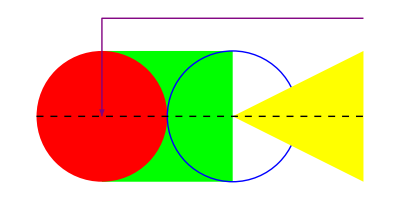
```mathematica
-Graphics-//ReadableForm
```

Graphics @ {
    RGBColor[ 0, 1, 0 ],
    Thickness @ Large,
    Rectangle[ { 0, -1 }, { 2, 1 } ],
    { RGBColor[ 1, 0, 0 ], Disk @ { 0, 0 } },
    { RGBColor[ 0, 0, 1 ], Circle @ { 2, 0 } },
    { RGBColor[ 1, 1, 0 ], Polygon @ { { 2, 0 }, { 4, 1 }, { 4, -1 } } },
    {
        RGBColor[ 0.5, 0, 0.5 ],
        Arrowheads @ Large,
        Arrow @ { { 4, 3 / 2 }, { 0, 3 / 2 }, { 0, 0 } },
        { GrayLevel[ 0 ], Dashing @ { Small, Small }, Line @ { { -1, 0 }, { 4, 0 } } }
    }
}

Visually inspect properties of formatted objects:

```mathematica
ResourceObject[…]//ReadableForm
```

ResourceObject[
    <|
        "Name" -> "LeNet Trained on MNIST Data",
        "UUID" -> "050b1a0a-f43a-4c28-b7e0-72607a918467",
        "ResourceType" -> "NeuralNet",
        "Version" -> "1.16.0",
        "Description" -> "Identify the handwritten digit in an image",
        "RepositoryLocation" ->
            URL[ "https://www.wolframcloud.com/objects/resourcesystem/api/1.0" ],
        "WolframLanguageVersionRequired" -> "11.1",
        "ContentElements" -> {
            "ConstructionNotebook",
            "ConstructionNotebookExpression",
            "EvaluationNet",
            "UninitializedEvaluationNet",
            "EvaluationExample"
        }
    |>,
    ResourceSystemBase -> "https://www.wolframcloud.com/objects/resourcesystem/api/1.0"
]

### Scope

Input-style syntax highlighting is used:

```mathematica
ReadableForm[Hold[f[x_]:=Table[i+1,{i,x}]]]
```

Hold[ f[ x_ ] := Table[ i + 1, { i, x } ] ]

Use Unevaluated to prevent the expression from evaluating:

```mathematica
ReadableForm[Unevaluated[Echo[∫_0^1 Log[1/2 (1+√(1+4 x))]/x ⅆx]]]
```

Echo @ Integrate[ Log[ (1 / 2) * (1 + Sqrt[ 1 + 4 * x ]) ] / x, { x, 0, 1 } ]

### Generalizations and Extensions

ToString will preserve the whitespace:

```mathematica
if=ReadableForm[TestResultObject[…]]
```

TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1 / 0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>

```mathematica
ToString[if]
```

TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1 / 0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>

CopyToClipboard will also preserve much of the formatting:

```mathematica
CopyToClipboard[if];
Paste[]
```

```mathematica
TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1 / 0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>
```

### Options

#### CachePersistence

With CachePersistence→None, ReadableForm will not use any caching, which reduces overall memory usage but is the slowest method:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->None]]]]
```

0.0192805

With the default behavior of CachePersistence→Automatic, ReadableForm will remember some values between evaluations to gain a modest performance boost:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->Automatic]]]]
```

0.0112235

Using CachePersistence→Full will give the fastest performance, but the extra memory used is not released for the remainder of the kernel session:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->Full]]]]
```

0.000142261

#### DynamicAlignment

ReadableForm can adjust indentation of certain parts of code in order to obtain alignment across lines when using a monospace font. Here is a helper function to display monospaced results:

```mathematica
showMonospace[expr_]:=Style[ToString[expr],PrivateFontOptions->{"OperatorSubstitution"->False},FontFamily->"Source Code Pro"];
```

```mathematica
showMonospace[expr=]
```

Hold[myFunction[] := Module[{result, anotherResult, test}, result = If[thisThing[], thenDoThatThing[], If[thisThing[], thenDoThatThing[], otherwiseDoSomethingElse[]]]; anotherResult = If[thisThing[], thenDoThatThing[], result = If[thisThing[], thenDoThatThing[], otherwiseDoSomethingElse[]]]; otherFunction[result, anotherResult, test]]]

By default, ReadableForm will only indent one step at a time:

```mathematica
ReadableForm[expr]//showMonospace
```

Hold[
    myFunction[ ] := 
        Module[ { result, anotherResult, test },
            
            result = 
                If[ thisThing[ ],
                    thenDoThatThing[ ],
                    If[ thisThing[ ],
                        thenDoThatThing[ ],
                        otherwiseDoSomethingElse[ ]
                    ]
                ];

            
            anotherResult = 
                If[ thisThing[ ],
                    thenDoThatThing[ ],
                    result = 
                        If[ thisThing[ ],
                            thenDoThatThing[ ],
                            otherwiseDoSomethingElse[ ]
                        ]
                ];

            otherFunction[ result, anotherResult, test ]
        ]
]

Use the setting "DynamicAlignment"→True to perform additional alignment heuristics:

```mathematica
ReadableForm[expr,"DynamicAlignment"->True]//showMonospace
```

Hold[
    myFunction[ ] := 
        Module[ { result, anotherResult, test },
            
            result = If[ thisThing[ ],
                         thenDoThatThing[ ],
                         If[ thisThing[ ],
                             thenDoThatThing[ ],
                             otherwiseDoSomethingElse[ ]
                         ]
                     ];

            
            anotherResult = If[ thisThing[ ],
                                thenDoThatThing[ ],
                                result = If[ thisThing[ ],
                                             thenDoThatThing[ ],
                                             otherwiseDoSomethingElse[ ]
                                         ]
                            ];

            otherFunction[ result, anotherResult, test ]
        ]
]

Align associations:

```mathematica
ReadableForm[TestResultObject[…],"DynamicAlignment"->True,PageWidth->150]//showMonospace
```

TestResultObject @ <|
    "TestClass"        -> None,
    "TestIndex"        -> 1,
    "TestID"           -> None,
    "Outcome"          -> "MessagesFailure",
    "Input"            -> HoldForm[ 1 / 0 ],
    "ExpectedOutput"   -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput"     -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages"   -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed"      -> Quantity[ 0., "Seconds" ],
    "MemoryUsed"       -> Quantity[ 1136, "Bytes" ]
|>

#### FormatHeads

By default, some expressions are formatted in StandardForm in order to enhance readability:

```mathematica
data=<|"Image"->RandomImage[1,{5,5}],"Time"->Now,"Graphics"->-Graphics-|>;
ReadableForm[data]
```

<|
    "Image" -> -Graphics-,
    "Time" -> "Wed 27 Apr 2022 12:06:38""GMT"-4,
    "Graphics" ->
        Graphics @ {
            RGBColor[ 0, 1, 0 ],
            Thickness @ Large,
            Rectangle[ { 0, -1 }, { 2, 1 } ],
            { RGBColor[ 1, 0, 0 ], Disk @ { 0, 0 } },
            { RGBColor[ 0, 0, 1 ], Circle @ { 2, 0 } },
            { RGBColor[ 1, 1, 0 ], Polygon @ { { 2, 0 }, { 4, 1 }, { 4, -1 } } },
            {
                RGBColor[ 0.5, 0, 0.5 ],
                Arrowheads @ Large,
                Arrow @ { { 4, 3 / 2 }, { 0, 3 / 2 }, { 0, 0 } },
                {
                    GrayLevel[ 0 ],
                    Dashing @ { Small, Small },
                    Line @ { { -1, 0 }, { 4, 0 } }
                }
            }
        }
|>

Use "FormatHeads" to control which expressions are formatted in StandardForm:

```mathematica
ReadableForm[data,"FormatHeads"->{Image,Graphics}]
```

<|
    "Image" -> -Graphics-,
    "Time" ->
        DateObject[
            { 2022, 4, 27, 12, 6, 38.2625574 },
            "Instant",
            "Gregorian",
            -4.
        ],
    "Graphics" -> -Graphics-
|>

Use Automatic to include the defaults:

```mathematica
ReadableForm[data,"FormatHeads"->{Automatic,Graphics}]
```

<| "Image" -> -Graphics-, "Time" -> "Wed 27 Apr 2022 12:06:38""GMT"-4, "Graphics" -> -Graphics- |>

#### IndentSize

Change the size of indentation in the output:

```mathematica
ReadableForm[SystemInformation["Small"],"IndentSize"->1,"FormatHeads"->None]
```

{
 "Kernel" -> {
  "SystemID" -> "Windows-x86-64",
  "ReleaseID" -> "13.1.0.0 (7716157, 2022042613717)",
  "CreationDate" ->
   DateObject[ { 2022, 4, 26, 4, 0, 38 }, "Instant", "Gregorian", -4. ]
 },
 "FrontEnd" -> {
  "OperatingSystem" -> "Windows",
  "ReleaseID" -> "13.1.0.0 (7716157, 202204267844)",
  "CreationDate" ->
   DateObject[ { 2022, 4, 26, 3, 24, 56 }, "Instant", "Gregorian", -4. ]
 }
}

#### InitialIndent

Specify an amount of additional indentation to apply to every line:

```mathematica
ReadableForm[<|"Test1"-><|"Name"->"First","Data"->Range[10]|>,"Test2"-><|"Name"->"Second","Data"->{}|>|>,"InitialIndent"->8]
```

<|
                                    "Test1" -> <|
                                        "Name" -> "First",
                                        "Data" -> { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 }
                                    |>,
                                    "Test2" -> <| "Name" -> "Second", "Data" -> { } |>
                                |>

#### PageWidth

Set a desired page width to control line breaks:

```mathematica
ReadableForm[SystemInformation["Small"],"PageWidth"->60,"FormatHeads"->None]
```

{
    "Kernel" -> {
        "SystemID" -> "Windows-x86-64",
        "ReleaseID" -> "13.1.0.0 (7716157, 2022042613717)",
        "CreationDate" ->
            DateObject[
                { 2022, 4, 26, 4, 0, 38 },
                "Instant",
                "Gregorian",
                -4.
            ]
    },
    "FrontEnd" -> {
        "OperatingSystem" -> "Windows",
        "ReleaseID" -> "13.1.0.0 (7716157, 202204267844)",
        "CreationDate" ->
            DateObject[
                { 2022, 4, 26, 3, 24, 56 },
                "Instant",
                "Gregorian",
                -4.
            ]
    }
}

#### PerformanceGoal

By default, ReadableForm will traverse expressions as deep as possible to apply formatting:

```mathematica
RepeatedTiming[ToString[ReadableForm[Unevaluated[],CachePersistence->None]]]
```

{0.00267465,PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First @ FirstPosition[ list, Max @ list ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /;
    AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            (Position[ list, #1 ] &) /@ DeleteDuplicates @ TakeLargest[ list, n ]
        ],
        n
    ]}

With PerformanceGoal→"Speed", ReadableForm traverses only deep enough to format lines and uses InputForm to handle the rest:

```mathematica
RepeatedTiming[ToString[ReadableForm[Unevaluated[],CachePersistence->None,PerformanceGoal->"Speed"]]]
```

{0.00133117,PositionLargest[list_List] /; AllTrue[list, NumericQ] := 
    First @ FirstPosition[list, Max[list]];

PositionLargest[list_List, n:_Integer | HoldPattern[UpTo][_Integer]] /;
    AllTrue[list, NumericQ] := 
    Take[
        Flatten[
            (Position[list, #1] &) /@ DeleteDuplicates @ TakeLargest[list, n]
        ],
        n
    ]}

#### PrefixForm

By default, ReadableForm will use Prefix formatting (f@expr) for some expressions:

```mathematica
ReadableForm[Unevaluated[]]
```

PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First @ FirstPosition[ list, Max @ list ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /;
    AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            (Position[ list, #1 ] &) /@ DeleteDuplicates @ TakeLargest[ list, n ]
        ],
        n
    ]

Disable Prefix formatting:

```mathematica
ReadableForm[Unevaluated[],"PrefixForm"->False]
```

PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First[ FirstPosition[ list, Max[ list ] ] ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /;
    AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            (Position[ list, #1 ] &) /@ DeleteDuplicates[ TakeLargest[ list, n ] ]
        ],
        n
    ]

#### RealAccuracy

By default, ReadableForm displays real numbers with all available digits:

```mathematica
ReadableForm[RandomReal[1000,5]]
```

{
    124.36079976848669,
    443.2298161259396,
    677.682966867234,
    954.2450596728177,
    840.0355668065201
}

Specify a maximum number of digits to display:

```mathematica
ReadableForm[RandomReal[1000,5],"RealAccuracy"->3]
```

{ 373.0, 715.0, 267.0, 942.0, 298.0 }

#### RelativeWidth

By default, measuring "PageWidth" per line includes the leading whitespace:

```mathematica
expr=<|
"Test1"-><|"Name"->"First","Data"->Range[10]|>,
"Test2"-><|"Name"->"Second","Data"->{}|>
|>;
ReadableForm[expr,"IndentSize"->12,"PageWidth"->45]
```

<|
            "Test1" -> <|
                        "Name" -> "First",
                        "Data" -> {
                                    1,
                                    2,
                                    3,
                                    4,
                                    5,
                                    6,
                                    7,
                                    8,
                                    9,
                                    10
                        }
            |>,
            "Test2" -> <|
                        "Name" -> "Second",
                        "Data" -> { }
            |>
|>

Set "RelativeWidth" to True if you don't want to count the leading whitespace:

```mathematica
ReadableForm[expr,"IndentSize"->12,"PageWidth"->45,"RelativeWidth"->True]
```

<|
            "Test1" -> <|
                        "Name" -> "First",
                        "Data" -> { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 }
            |>,
            "Test2" -> <| "Name" -> "Second", "Data" -> { } |>
|>

### Applications

#### Copy Formatted Expressions

Copy expressions to the clipboard that will be formatted nicely when pasting into email, etc.:

```mathematica
SystemInformation["Small"]//ReadableForm//CopyToClipboard;
Paste[]
```

```mathematica
{
    "Kernel" -> {
        "SystemID" -> "Windows-x86-64",
        "ReleaseID" -> "13.1.0.0 (7716157, 2022042613717)",
        "CreationDate" ->
            DateObject[ { 2022, 4, 26, 4, 0, 38 }, "Instant", "Gregorian", -4. ]
    },
    "FrontEnd" -> {
        "OperatingSystem" -> "Windows",
        "ReleaseID" -> "13.1.0.0 (7716157, 202204267844)",
        "CreationDate" ->
            DateObject[ { 2022, 4, 26, 3, 24, 56 }, "Instant", "Gregorian", -4. ]
    }
}
```

#### Readable Log Files

```mathematica
DeleteFile["log.txt"];
$Line=0;
```

Create readable log files with lots of metadata:

```mathematica
logEvent[event_]:=
PutAppend[ReadableForm[<|"Time"->DateString[],"Event"->event,"Metadata"->ResourceFunction["SessionInformation"][]|>,"FormatHeads"->None,PageWidth->70],"log.txt"];
```

```mathematica
logEvent["A thing just happened"]
```

```mathematica
FilePrint["log.txt"]
```

<|
    "Time" -> "Wed 27 Apr 2022 12:11:49",
    "Event" -> "A thing just happened",
    "Metadata" -> <|
        "$ByteOrdering" -> -1,
        "$CloudBase" -> "https://www.wolframcloud.com/",
        "$CloudVersion" -> "1.62 (April 8, 2022)",
        "$CommandLine" -> {
            "WolframKernel",
            "-wstp",
            "-noicon",
            "-linkprotocol",
            "SharedMemory",
            "-linkmode",
            "connect",
            "-linkname",
            "rn3uy_shm"
        },
        "$Context" -> "Global`",
        "$ContextPath" -> {
            "DocumentationSearch`",
            "ResourceLocator`",
            "RH`",
            "RHLoader`",
            "NaturalLanguageProcessingLoader`",
            "System`",
            "Global`"
        },
        "$CreationDate" ->
            DateObject[
                { 2022, 4, 26, 4, 0, 38 },
                "Instant",
                "Gregorian",
                -4.
            ],
        "$EvaluationCloudObject" -> None,
        "$EvaluationEnvironment" -> "Session",
        "$KernelID" -> 0,
        "$Line" -> 2,
        "$MachineName" -> "galapagos",
        "$MachineType" -> "PC",
        "$MessageList" -> { },
        "$Notebooks" -> True,
        "$OperatingSystem" -> "Windows",
        "$ParentLink" -> LinkObject[ "rn3uy_shm", 3, 1 ],
        "$ParentProcessID" -> 0,
        "$ProcessID" -> 28540,
        "$ProcessorType" -> "x86-64",
        "$ReleaseNumber" -> 0,
        "$RequesterAddress" -> None,
        "$RequesterWolframID" -> "richardh@wolfram.com",
        "$RequesterWolframUUID" -> "fae3ac93-4e18-4708-9aba-2dfa705f2337",
        "$SessionID" -> 34028886145147528536,
        "$System" -> "Microsoft Windows (64-bit)",
        "$SystemCharacterEncoding" -> "WindowsANSI",
        "$SystemID" -> "Windows-x86-64",
        "$UserAgentString" -> None,
        "$UserName" -> "rhennigan",
        "$Version" -> "13.1.0 for Microsoft Windows (64-bit) (April 26, \
2022)",
        "$VersionNumber" -> 13.1,
        "$WolframID" -> "richardh@wolfram.com",
        "$WolframUUID" -> "fae3ac93-4e18-4708-9aba-2dfa705f2337",
        "DefinitionCreationDate" ->
            DateObject[
                { 2018, 10, 11, 22, 14, 23.1626366 },
                "Instant",
                "Gregorian",
                0.
            ],
        "HTTPRequestData" -> None,
        "NotebookInformation" -> {
            "FileName" ->
                FrontEnd`FileName[
                    {
                        $RootDirectory,
                        "H:",
                        "Documents",
                        "ResourceFunctions",
                        "Definitions",
                        "ReadableForm"
                    },
                    "Examples.nb",
                    CharacterEncoding -> "UTF-8"
                ],
            "FileModificationTime" -> 3.860063169*^9,
            "WindowTitle" -> "Examples.nb",
            "MemoryModificationTime" -> 3.860064707128766*^9,
            "ModifiedInMemory" -> True,
            "StorageSystem" -> "Local",
            "DocumentType" -> "Notebook",
            "MIMEType" -> "application/vnd.wolfram.nb",
            "StyleDefinitions" -> {
                NotebookObject[
                    FrontEndObject @ LinkObject[ "rn3uy_shm", 3, 1 ],
                    21
                ]
            },
            "ExpressionUUID" -> "0c95abc5-f093-4791-9e3f-7a08a3411123"
        },
        "NotebookTaggingRules" -> <|
            "InformationPopupMenuItemAdded" -> True,
            "AutoUpdate" -> True,
            "NotebookIndexQ" -> True,
            "NotebookLastIndexed" ->
                DateObject[
                    { 2022, 4, 27, 12, 2, 11.3449166 },
                    "Instant",
                    "Gregorian",
                    -4.
                ],
            "NotebookUUID" -> "0c95abc5-f093-4791-9e3f-7a08a3411123"
        |>,
        "SessionTime" -> Quantity[ 0.41221083333333336, "Hours" ],
        "Stack" -> {
            StackComplete,
            logEvent,
            PutAppend,
            ReadableForm,
            Association,
            List,
            Rule,
            \
FunctionRepository`$8d26141d7e37414189b2e4b3b7bcfd3a`SessionInformation
        },
        "Timestamp" ->
            DateObject[
                { 2022, 4, 27, 16, 11, 49.057183 },
                "Instant",
                "Gregorian",
                0.
            ]
    |>
|>

#### Generate Formatted Packages

ReadableForm can be used to convert a FullDefinition into a formatted package notebook. Here's an example from a resource function:

```mathematica
defString=Block[{$ContextPath=Prepend[$ContextPath,ResourceFunction["Stereogram3D","Context"]]},ToString[FullDefinition[ResourceFunction["Stereogram3D"]],InputForm]];
```

View the default formatting:

```mathematica
Snippet[defString,20]
```

Stereogram3D[gfx_, opts:OptionsPattern[{Stereogram3D, Graphics3D, Rasterize,
GeoGraphics}]] := Stereogram3D[gfx, Automatic, opts]
 
Stereogram3D[Graphics3D[items_, gfxOpts___], form_,
opts:OptionsPattern[{Stereogram3D, Graphics3D, Rasterize, GeoGraphics}]] :=
Stereogram3D[Flatten[{items}], form, opts, gfxOpts]
 
Stereogram3D[items_List, form_, opts:OptionsPattern[{Stereogram3D, Graphics3D,
Rasterize, GeoGraphics}]] := Module[{vp, va, vv, vc, div, size, view, res}, vp =
toViewPoint[OptionValue[ViewPoint]]; va = toViewAngle[OptionValue[ViewAngle]];
vv = toViewVertical[OptionValue[ViewVertical]]; vc =
toViewCenter[OptionValue[ViewCenter]]; div =
toDivergence[OptionValue[Divergence]]; size =
toImageSize[OptionValue[ImageSize]]; view = Sequence[vp, va, vv, vc, div, size];
res = Catch[stereogram3D[form, items, view, opts], $tag]; res /; res =!= $fail]
 
Stereogram3D[other_, form_, opts:OptionsPattern[{Stereogram3D, Graphics3D,
Rasterize, GeoGraphics}]] := Module[{tryShow}, tryShow = Quiet[Show[other]];
If[MatchQ[tryShow, Blank[Graphics3D]], Stereogram3D[tryShow, form, opts],
Stereogram3D[Graphics3D[other], form, opts]]]

Create formatted cells using ReadableForm:

```mathematica
cells=Cases[ToExpression[defString,InputForm,HoldComplete],e:Except[Null]:>Cell[BoxData[ToBoxes[ReadableForm[Unevaluated[e]]]],"Code"]];
```

Display in a package notebook:

```mathematica
NotebookPut@Notebook[cells,StyleDefinitions->"Package.nb"]
```

hwsf4_shm284FrontEndObject[LinkObject["hwsf4_shm", 3, 1]]284Untitled-25

-Graphics-

#### Create a Formatter Palette

Create a function to format notebook boxes:

```mathematica
$lb=_String?(StringMatchQ[WhitespaceCharacter...~~"\n"|FromCharacterCode[62371]~~WhitespaceCharacter...]);
```

```mathematica
formatBoxes[RowBox[lines:{___,$lb,___}]]:=Enclose[Riffle[(Confirm@*formatBoxes)/@DeleteCases[lines,$lb],"\n"]];
```

```mathematica
formatBoxes[boxes_]:=Enclose[Replace[Confirm[Replace[MakeExpression[StripBoxes[boxes],StandardForm],_ErrorBox->$Failed]],HoldComplete[e_]:>Replace[ToBoxes[ReadableForm[Unevaluated[e],"DynamicAlignment"->True],StandardForm],StyleBox[b_,___]:>b]]];
```

Create a button that formats the boxes representing the current selection:

```mathematica
formatSelection[nbo_NotebookObject]:=Enclose[NotebookWrite[nbo,Confirm[formatBoxes[StripBoxes[NotebookRead[nbo]]]]],MessageDialog["The current selection does not contain a valid expression."]&];
```

```mathematica
sel=Button["Format Selection",formatSelection[InputNotebook[]],Method->"Queued"]
```

Format Selection

Create another button that formats cells:

```mathematica
formatCell[cell_CellObject]:=(
SelectionMove[cell,All,CellContents]; 
formatSelection[ParentNotebook[cell]]
);

formatCell[cells:{___CellObject}]:=
formatCell/@(ResourceFunction["SelectByCurrentValue"][cells,CellStyle,MemberQ["Input"|"Code"]]);
```

```mathematica
cell=Button["Format Cells",formatCell[SelectedCells[InputNotebook[]]],Method->"Queued"]
```

Format Cells

Create one more button to format an entire notebook:

```mathematica
nb=Button["Format Notebook",formatCell[Cells[InputNotebook[]]],Method->"Queued"]
```

Format Notebook

Combine into a single palette:

```mathematica
CreatePalette[Column[{sel,cell,nb}],WindowTitle->"Formatter"]
```

6hmdd_shm113FrontEndObject[LinkObject["6hmdd_shm", 3, 1]]113Formatter

Test on an example notebook:

```mathematica
NotebookOpen[FindFile["ExampleData/document.nb"]]
```

6hmdd_shm112FrontEndObject[LinkObject["6hmdd_shm", 3, 1]]112document.nbC:\Program Files\Wolfram Research\Mathematica\13.1\Documentation\English\System\ExampleData\document.nb

### Properties and Relations

For expressions that only require a single line to display, the output will be very similar to InputForm:

```mathematica
InputForm[x √5+y^2+1/z]
```

Sqrt[5]*x + y^2 + z^(-1)

```mathematica
ReadableForm[x √5+y^2+1/z]
```

Sqrt[5] * x + y^2 + z^(-1)

### Possible Issues

ReadableForm is just a formatting wrapper; it doesn't evaluate on its own:

```mathematica
FullForm[ReadableForm[x]]
```

ReadableForm[x]

The head is not visible to InputForm:

```mathematica
InputForm[ReadableForm[x]]
```

x

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

pretty print

input

code

formatting

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

InputForm

FullForm

StandardForm

CopyToClipboard

### Related Resource Objects

ToFullString

PrettyForm

SaveReadableNotebook

### Source/Reference Citation

Source, reference or citation information

### Links

ReadableForm | rhennigan/ResourceFunctions | GitHub

### Tests

```mathematica
VerificationTest[
    verifyExpr // ClearAll;
    verifyExpr // Attributes = { HoldAllComplete };
    verifyExpr[ expr_, opts___ ] :=
        Module[ { string, readable },
            string   = ToString[ HoldComplete @ expr, InputForm ];
            readable = ToString @ ReadableForm[ HoldComplete @ expr, opts ];
            SameQ[
                ToExpression[ string, InputForm, HoldComplete ],
                ToExpression[ readable, InputForm, HoldComplete ]
            ]
        ],
    Null
]
```

#### Regression tests

##### Verify round trips

```mathematica
VerificationTest[
    verifyExpr[
        Hold[ Times[ a, -1 ], Times[ -1, a ] ]
    ]
]
```

```mathematica
VerificationTest[
    verifyExpr @ <|
        "Context" -> ($Context = ctx),
        "ContextPath" -> ($ContextPath = cp)
    |>
]
```

```mathematica
VerificationTest[
    verifyExpr @ Hold @ Plus[
        a,
        Times[
            -1,
            Plus[ Times[ -1, f[ Plus[ b, 1 ] ] ] ]
        ]
    ]
]
```

```mathematica
VerificationTest[
    verifyExpr @ Function[ Times[ Slot[1], -1 ] ]
]
```

```mathematica
VerificationTest @ verifyExpr[
    HoldComplete @ Association @ Apply[
        Rule,
        Tally[ Part[ Part[ preformated, All, 4 ], All, 2 ] ],
        { 1 }
    ],
    PageWidth -> 65,
    "DynamicAlignment" -> True,
    "StrictMode" -> True
]
```

```mathematica
VerificationTest @ verifyExpr @ Apply[ Set, x, { 1 } ]
```

```mathematica
VerificationTest @ verifyExpr @ MapApply[ Set, x ]
```

```mathematica
VerificationTest @ verifyExpr @ <| "a" -> 1, "b" -> 2, "a" -> 3 |>;
```

##### Expected outputs

```mathematica
VerificationTest[
    ToString @ ReadableForm[
        Unevaluated[
            a - (b + c) - d + e
        ],
        "DynamicAlignment" -> True,
        PageWidth -> 30
    ],
    "a - (b + c) - d + e"
]
```

```mathematica
VerificationTest[
    ToString @ ReadableForm @ Hold @ Association @ stuff,
    "Hold @ Association @ stuff"
]
```

```mathematica
VerificationTest[
    ToString @ ReadableForm @ Hold[ Now - Quantity[ 12, "Hours" ] ],
    "Hold[ Now - Quantity[ 12, \"Hours\" ] ]"
]
```

```mathematica
VerificationTest[
    ToString @ ReadableForm @ Hold @ x[[ 1, 2;;3;;4 ]],
    "Hold @ x[[ 1, 2;;3;;4 ]]"
]
```

```mathematica
VerificationTest[
    ToString @ ReadableForm @ Unevaluated[
        $checkPropertyOptions = <|
            "DefinitionNotebook" -> {
                "IgnoredProperties" -> {
                    "DefinitionNotebook",
                    "FileManagerData",
                    "PacletFiles",
                    "PacletObject"
                }
            },
            "Documentation" -> { "ScrapedProperties" -> { "Documentation" } },
            "PacletFiles" -> {
                "ScrapedProperties" -> {
                    "PacletFiles",
                    "PacletObject",
                    "Name",
                    "Description",
                    "ContributorInformation"
                }
            }
        |>;
    ],
    "\
$checkPropertyOptions = <|
    \"DefinitionNotebook\" -> {
        \"IgnoredProperties\" -> {
            \"DefinitionNotebook\",
            \"FileManagerData\",
            \"PacletFiles\",
            \"PacletObject\"
        }
    },
    \"Documentation\" -> { \"ScrapedProperties\" -> { \"Documentation\" } },
    \"PacletFiles\" -> {
        \"ScrapedProperties\" -> {
            \"PacletFiles\",
            \"PacletObject\",
            \"Name\",
            \"Description\",
            \"ContributorInformation\"
        }
    }
|>;"
]
```

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.